# GR tests based on amplitudes and phases

```mathematica
Quit[]
```

## Load packages

```mathematica
Which[$SystemID=="MacOSX-x86-64",Get["/Users/xisco/git/ah-overtones-project/codes/RDownCode/RDown.m"],$SystemID=="Linux-x86-64",Get["/work/francisco.jimenez/RDFits/RDown.m"]]
```

```mathematica
Print["Starting Python session." ,session = StartExternalSession[{"Python","Version"->"3"}]];
ExternalEvaluate[session, "import qnm; import pycbc ;import h5py;from dynesty.utils import resample_equal; import numpy as np; from qnm.schwarzschild.overtonesequence import SchwOvertoneSeq as schw"];
```

Starting Python session.ExternalSessionObject[…]

## Setup plot style and extra functions

### Setup paths and other notebook folders

```mathematica
dir="~/Desktop/RDFits_330/";
```

```mathematica
markers={"●","■","◆","▲","▼","○","□","◇","△","▽"};
```

```mathematica
colors={RGBColor[0.,0.62,0.53],RGBColor[1.,0.,0.38],RGBColor[0.,0.73,1.],RGBColor[1.,0.71,0.],RGBColor[0.46,0.,0.62],RGBColor[0.68,0.69,0.],RGBColor[0.62,0.,0.13],RGBColor[1.,0.53,0.25],RGBColor[0.,0.62,0.53],RGBColor[1.,0.,0.38],RGBColor[0.,0.73,1.],RGBColor[1.,0.71,0.],RGBColor[0.46,0.,0.62],RGBColor[0.68,0.69,0.],RGBColor[0.62,0.,0.13],RGBColor[1.,0.53,0.25]}
```

{RGBColor[0., 0.62, 0.53],RGBColor[1., 0., 0.38],RGBColor[0., 0.73, 1.],RGBColor[1., 0.71, 0.],RGBColor[0.46, 0., 0.62],RGBColor[0.68, 0.69, 0.],RGBColor[0.62, 0., 0.13],RGBColor[1., 0.53, 0.25],RGBColor[0., 0.62, 0.53],RGBColor[1., 0., 0.38],RGBColor[0., 0.73, 1.],RGBColor[1., 0.71, 0.],RGBColor[0.46, 0., 0.62],RGBColor[0.68, 0.69, 0.],RGBColor[0.62, 0., 0.13],RGBColor[1., 0.53, 0.25]}

### Spherical harmonics Yslm

```mathematica
Eth[n_,f_] := - Sin[t]^n (D[f/Sin[t]^n,t]+I D[f/Sin[t]^n,p]/Sin[t])
Yp1[l_,m_]:= FullSimplify[Sqrt[ (l-1)!/(l+1)!]Eth[0,SphericalHarmonicY[l,m,t,p]]]
Yp2[l_,m_]:= FullSimplify[Sqrt[ (l-2)!/(l+2)!]Eth[1,Eth[0,SphericalHarmonicY[l,m,t,p]]]]

Ethbar[n_,f_] := - Sin[t]^(-n) (D[f Sin[t]^n,t]-I D[f Sin[t]^n,p]/Sin[t])
Ym1[l_,m_]:= FullSimplify[Sqrt[ (l-1)!/(l+1)!](-1)^(-1) Ethbar[0,SphericalHarmonicY[l,m,t,p]]]
Ym2[l_,m_]:= FullSimplify[Sqrt[ (l-2)!/(l+2)!](-1)^(-2)Ethbar[-1,Ethbar[0,SphericalHarmonicY[l,m,t,p]]]]
```

```mathematica
(* same source, direct formula using Wigner d-functions *)
wd[n_,l_,m_]:=Sum[
(-1)^i  Sqrt[(l+m)! (l-m)! (l+n)! (l-n)!] / ((l+m-i)!(l-n-i)!i!(i+n-m)!)
Cos[t/2]^(2l+m-n-2i)Sin[t/2]^(2i+n-m),
{i,Max[0,m-n],Min[l+m,l-n]}
]
Ydirect[n_,l_,m_]:=FullSimplify[(-1)^n  Sqrt[(2l+1)/(4Pi)] wd[-n,l,m]E^(I m p)]
```

```mathematica
WaveCombine[wave_,modes_,θ_:0,ϕ_:0,zeroalign_:True]:=Module[{yharm,res,restdomain,tmax},

res=Sum[yharm=Ydirect[-2,modes[[i,1]],modes[[i,2]]]/.t->θ/.p->ϕ; yharm*wave[[i,All,2]],{i,Length@modes}];
restdomain=Transpose[{wave[[1,All,1]],res}];

If[zeroalign,tmax=TimeOfMaximum[restdomain[[Round[(Length@restdomain)/2] ;; -1]]];

Return[Transpose[{restdomain[[All,1]]-tmax,restdomain[[All,2]]}]],Return[restdomain]];
]
```

### Old fits to amplitude and phase

```mathematica
phase[qq_,t_,w330_,w220_]:=2.551092133630567+8.355670911569911/(8.839571559719866+qq^2)-(w330-w220)t
a330[qq_]:=0.4367931773176181+0.005824901860357143/qq^3+0.14604066055320677/qq^2-0.588658739731182/qq
```

## Load NR data

### SXS

```mathematica
join=False;
sxsdir="/Users/xisco/mount/Atlas/SXS/data";
sxsdir="/Users/xisco/SXS/SXS_New"
sxsdirs=Select[FileNames["*",sxsdir],DirectoryQ[#]&];
```

/Users/xisco/SXS/SXS_New

```mathematica
posl300=Flatten@Position[ToExpression[(StringSplit[#,"_"]&/@sxsdirs)[[All,-1]]],_?(#>=300&)];
sxsdirsl300=sxsdirs[[posl300]];
sxsdirsl300=sxsdirs;
```

```mathematica
mysxscase=SXSParClassification[sxsdirs,{{"Non-Precessing"},{"χ1","#<0.01"},{"χ2","#<0.01"}},"Verbose"->True,"MetadataType"->"txt","Mass1-Str"->"reference-mass1","Mass2-Str"->"reference-mass2"];
(*mysxscase=SXSParClassification[sxsdirsl300,{{"Non-Precessing"},{"χ1","#<0.5"},{"χ2","#<0.5"},{"eccentricity","#<0.01"}},"Verbose"->True,"MetadataType"->"json","Mass1-Str"->"reference-mass1","Mass2-Str"->"reference-mass2"]*)
(*mysxscase=SXSParClassification[sxsdirsl300,{{"Non-Precessing"},{"MassRatio","1.9<#<2.5"},{"χ1","#<0.5"},{"χ2","#<0.5"},{"eccentricity","#<0.01"},{"Final-Spin","0.8<#<0.9"}},"Verbose"->True,"MetadataType"->"json"]*)
(*mysxscase=SXSParClassification[sxsdirsl300,{{"eccentricity","#<0.01"},{"MassRatio","1.2<#<2.5"},{"Final-Spin","0.8<#<0.9"}},"Verbose"->True,"MetadataType"->"json"]*)
modes={{2,2},{2,1},{3,3},{4,4}}
```

Classification Input Variables. Examples: {{'MassRatio', '0.99<#<1.1'}},{{'Distance', '#>16'}},{{'Orbits', '#>25'}},{{'Precessing'}},
{{'CBCType','BHBH'},{'Non-Precessing'}},{{'High-Spin'}},{{'χeff','#>0.6'}},{{'χ1','#>0.6'}},{{'χ2','#>0.6'}},{{'Unequal'}}

Take care! Some of the sxs file names are not consistent with the metadata files

The spin definition is consitent with 'initial-spin' values and not relaxed ones

The mass definition is consitent with 'initial-mass' values and not relaxed ones

Case | q | χ1 | χ2 | D | e | simulation name
/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0E1 | 1. | {0., 0., 0.} | {0., 0., 0.} | 18.000100000000000 | reference_eccentricity | {{d18.0_q1.0_s0_0_0_s0_0_0E1/Lev5}}
/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0Ecc6 | 1. | {0., 0., 0.} | {0., 0., 0.} | 18.000000000000000 | reference_eccentricity | {{d18.0_q1.0_s0_0_0_s0_0_0Ecc6/Lev5}}
/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0F1 | 1. | {0., 0., 0.} | {0., 0., 0.} | 18.000000000000000 | reference_eccentricity | {{d18.0_q1.0_s0_0_0_s0_0_0Ecc6/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0 | 1.2 | {0., 0., 0.} | {0., 0., 0.} | 12.671936035200000 | reference_eccentricity | {{BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0/Lev3}}
/Users/xisco/SXS/SXS_New/d18.0_q1.5_s0_0_0_s0_0_0 | 1.5 | {0., 0., 0.} | {0., 0., 0.} | 18.000000000000000 | reference_eccentricity | {{d18.0_q1.5_s0_0_0_s0_0_0/Lev6}}
/Users/xisco/SXS/SXS_New/BBH_SKS_d15.6_q1.83_sA_0_0_0_sB_0_0_0 | 1.8 | {0., 0., 0.} | {0., 0., 0.} | 15.550781250000000 | reference_eccentricity | {{BBH_SKS_d15.6_q1.83_sA_0_0_0_sB_0_0_0/Lev3}}
/Users/xisco/SXS/SXS_New/d13_q2_sA_0_0_0_sB_0_0_0 | 2. | {0., 0., 0.} | {0., 0., 0.} | 13.873799999999999 | reference_eccentricity | {{d13_q2_sA_0_0_0_sB_0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_SKS_d15_q2.32_sA_0_0_0_sB_0_0_0 | 2.3 | {0., 0., 0.} | {0., 0., 0.} | 15.000000000000000 | reference_eccentricity | {{BBH_SKS_d15_q2.32_sA_0_0_0_sB_0_0_0/Lev3}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d16.9_q2.50_sA_0_0_0_sB_0_0_0 | 2.5 | {0., 0., 0.} | {0., 0., 0.} | 16.899999999999999 | reference_eccentricity | {{BBH_CFMS_d16.9_q2.50_sA_0_0_0_sB_0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_SKS_d15.5_q2.51_sA_0_0_0_sB_0_0_0 | 2.5 | {0., 0., 0.} | {0., 0., 0.} | 15.500000000000000 | reference_eccentricity | {{BBH_SKS_d15.5_q2.51_sA_0_0_0_sB_0_0_0/Lev3}}
/Users/xisco/SXS/SXS_New/SXS_BBH_0259 | 2.5 | {0., 0., 0.} | {0., 0., 0.} | 16.899999999999999 | reference_eccentricity | {{BBH_CFMS_d16.9_q2.50_sA_0_0_0_sB_0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_SKS_d16.2_q3_sA_0_0_0_sB_0_0_0 | 3. | {0., 0., 0.} | {0., 0., 0.} | 16.199999999999999 | reference_eccentricity | {{BBH_SKS_d16.2_q3_sA_0_0_0_sB_0_0_0/Lev4}}
/Users/xisco/SXS/SXS_New/d14.0_q3.0_s0_0_0_s0_0_0 | 3. | {0., 0., 0.} | {0., 0., 0.} | 14.000000000000000 | reference_eccentricity | {{d14.0_q3.0_s0_0_0_s0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0 | 3.5 | {0., 0., 0.} | {0., 0., 0.} | 15.900000000000000 | reference_eccentricity | {{BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0/Lev4}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0 | 4. | {0., 0., 0.} | {0., 0., 0.} | 12.565200000000001 | reference_eccentricity | {{BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0/Lev4}}
/Users/xisco/SXS/SXS_New/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0 | 4. | {0., 0., 0.} | {0., 0., 0.} | 15.199999999999999 | reference_eccentricity | {{BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev4}}
/Users/xisco/SXS/SXS_New/d15.0_q5.0_s0_0_0_s0Ecc2em3 | 5. | {0., 0., 0.} | {0., 0., 0.} | 15.000000000000000 | reference_eccentricity | {{d15.0_q5.0_s0_0_0_s0Ecc2em3/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d14.5_q5.50_sA_0_0_0_sB_0_0_0 | 5.5 | {0., 0., 0.} | {0., 0., 0.} | 14.500000000000000 | reference_eccentricity | {{BBH_CFMS_d14.5_q5.50_sA_0_0_0_sB_0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0 | 6. | {0., 0., 0.} | {0., 0., 0.} | 14.000000000000000 | reference_eccentricity | {{BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0/Lev4}}
/Users/xisco/SXS/SXS_New/d13_q6_sA_0_0_0_sB_0_0_0 | 6. | {0., 0., 0.} | {0., 0., 0.} | 13.000000000000000 | reference_eccentricity | {{d13_q6_sA_0_0_0_sB_0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0 | 7. | {0., 0., 0.} | {0., 0., 0.} | 12.199999999999999 | reference_eccentricity | {{BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.5_q8.27_sA_0_0_0_sB_0_0_0 | 8.3 | {0., 0., 0.} | {0., 0., 0.} | 12.500000000000000 | reference_eccentricity | {{BBH_CFMS_d12.5_q8.27_sA_0_0_0_sB_0_0_0/Lev3}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0 | 9. | {0., 0., 0.} | {0., 0., 0.} | 11.400000000000000 | reference_eccentricity | {{BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0/Lev5}}
/Users/xisco/SXS/SXS_New/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0 | 10. | {0., 0., 0.} | {0., 0., 0.} | 13.000000000000000 | reference_eccentricity | {{BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0/Lev4}}

{{2,2},{2,1},{3,3},{4,4}}

```mathematica
mysxscaserh=Table[FileNames["*rhO*",mysxscase[[i]],2][[-1]],{i,Length@mysxscase}]
mysxscasemetafile=Flatten[Table[FileNames["metadata.txt",FileNameDrop[mysxscaserh[[i]],-2],2][[-1]],{i,Length@mysxscaserh}]]
(*mysxscasemetafile=Flatten[Table[FileNames["metadata.json",FileNameDrop[mysxscaserh[[i]],-1],2][[-1]],{i,Length@mysxscaserh}]]*)
```

{/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0E1/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0Ecc6/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0F1/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/d18.0_q1.5_s0_0_0_s0_0_0/Lev6/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_SKS_d15.6_q1.83_sA_0_0_0_sB_0_0_0/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/d13_q2_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_SKS_d15_q2.32_sA_0_0_0_sB_0_0_0/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d16.9_q2.50_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_SKS_d15.5_q2.51_sA_0_0_0_sB_0_0_0/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/SXS_BBH_0259/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_SKS_d16.2_q3_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/d14.0_q3.0_s0_0_0_s0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/d15.0_q5.0_s0_0_0_s0Ecc2em3/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d14.5_q5.50_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/d13_q6_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.5_q8.27_sA_0_0_0_sB_0_0_0/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/SXS_New/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5}

{/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0E1/metadata.txt,/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0Ecc6/metadata.txt,/Users/xisco/SXS/SXS_New/d18.0_q1.0_s0_0_0_s0_0_0F1/Lev5/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/d18.0_q1.5_s0_0_0_s0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_SKS_d15.6_q1.83_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/d13_q2_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_SKS_d15_q2.32_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d16.9_q2.50_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_SKS_d15.5_q2.51_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/SXS_BBH_0259/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_SKS_d16.2_q3_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/d14.0_q3.0_s0_0_0_s0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/d15.0_q5.0_s0_0_0_s0Ecc2em3/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d14.5_q5.50_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/d13_q6_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d12.5_q8.27_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/SXS_New/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0/metadata.txt}

```mathematica
(* For txt *)
mysxscasemetadata=SXSMetaFilesToRules/@mysxscasemetafile;
Print["tag = ",tag="alternative-names"/.mysxscasemetadata]
Print[" initial position 1 = ", ip1="initial-position1"/.mysxscasemetadata];
Print[" initial position 2 = ", ip2="initial-position2"/.mysxscasemetadata];
Print["mass1 = ",mass1=Flatten[("initial-mass1"/.mysxscasemetadata),1]]
Print["mass2 = ",mass2=Flatten[("initial-mass2"/.mysxscasemetadata),1]]
Print["χ1 = ",χ1=Chop
[(("initial-dimensionless-spin1"/.mysxscasemetadata)[[All,-1]])]]
Print["χ2 = ",χ2=Chop[(("initial-dimensionless-spin2"/.mysxscasemetadata)[[All,-1]])]]
Print["χeff = ",χeff=χ1*mass1+χ2*mass2]
Print["m1/m2 = ",q=mass1/mass2]
Print["m1·m2 = ",η=q/(1+q)^2*1.]
Print["af = ",af=("remnant-dimensionless-spin"/.mysxscasemetadata)[[All,-1]]]
Print["mf = ",mf=("remnant-mass"/.mysxscasemetadata)]
Print["kick = ", vr=("remnant-velocity"/.mysxscasemetadata) ]
```

tag = {{SXS:BBH:0066},{SXS:BBH:0070},{SXS:BBH:0070},{PRIVATE:BBH:0198,SXS:BBH:1143},{SXS:BBH:0007},{SXS:BBH:1354},{SXS:BBH:0169},{PRIVATE:BBH:0140,SXS:BBH:0201},{PRIVATE:BBH:0121,SXS:BBH:0259},{PRIVATE:BBH:0013,SXS:BBH:0191},{PRIVATE:BBH:0121,SXS:BBH:0259},{PRIVATE:BBH:0155,SXS:BBH:1221},{SXS:BBH:0030},{PRIVATE:BBH:0120,SXS:BBH:0294},{PRIVATE:BBH:0127,SXS:BBH:0182},{PRIVATE:BBH:0157,SXS:BBH:1220},{SXS:BBH:0107},{PRIVATE:BBH:0118,SXS:BBH:0296},{PRIVATE:BBH:0139,SXS:BBH:0181},{SXS:BBH:0166},{PRIVATE:BBH:0115,SXS:BBH:0298},{PRIVATE:BBH:0001,SXS:BBH:0186},{PRIVATE:BBH:0160,SXS:BBH:0301},{PRIVATE:BBH:0002,SXS:BBH:1107}}

initial position 1 = {{9.00005,5.53122×10^-9,0.},{9.,-4.89861×10^-8,0.},{9.,-4.89861×10^-8,0.},{5.63182,0.010292,0.},{7.19335,0.00787386,0.},{5.49724,0.0188405,-1.23496×10^-9},{4.61508,0.0137278,0.},{4.52254,0.0294442,0.},{4.81678,0.0147843,0.},{4.41845,0.0305029,0.},{4.81678,0.0147843,0.},{4.04912,0.032136,0.},{3.48807,0.0173463,0.},{3.52075,0.0167228,0.},{2.50152,0.018686,0.},{3.0388,0.0340084,0.},{2.48818,0.0165948,0.},{2.21952,0.016425,0.},{1.99857,0.0323939,0.},{1.84673,0.0167951,0.},{1.51559,0.0162453,0.},{1.34011,0.0147891,0.},{1.13214,0.014746,0.},{1.17394,0.0130301,0.}}

initial position 2 = {{-9.00005,5.53122×10^-9,0.},{-9.,-4.89861×10^-8,0.},{-9.,-4.89861×10^-8,0.},{-7.04011,0.010292,0.},{-10.806649767081623,0.00787386,0.},{-10.053540720267829,0.0188405,-1.23496×10^-9},{-9.25872,0.0137278,0.},{-10.47745591302693,0.0294442,0.},{-12.083220217034569,0.0147843,0.},{-11.081546695045166,0.0305029,0.},{-12.083220217034569,0.0147843,0.},{-12.1508796234128,0.032136,0.},{-10.511931936875811,0.0173463,0.},{-12.379251964161494,0.0167228,0.},{-10.063676013379833,0.018686,0.},{-12.161203428892502,0.0340084,0.},{-12.511817148652973,0.0165948,0.},{-12.28048300802452,0.016425,0.},{-12.001434337873228,0.0323939,0.},{-11.1533,0.0167951,0.},{-10.68441006457101,0.0162453,0.},{-11.159894396079205,0.0147891,0.},{-10.267857227700507,0.014746,0.},{-11.82606172393236,0.0130301,0.}}

mass1 = {0.5,0.5,0.5,0.555556,0.6,0.646893,0.666667,0.698455,0.714286,0.714897,0.714286,0.75,0.75,0.777778,0.8,0.8,0.833333,0.846154,0.857144,0.857143,0.875,0.892096,0.9,0.909091}

mass2 = {0.5,0.5,0.5,0.444444,0.4,0.353107,0.333333,0.301545,0.285714,0.285103,0.285714,0.25,0.25,0.222222,0.2,0.2,0.166667,0.153846,0.142858,0.142857,0.125,0.107904,0.1,0.0909091}

χ1 = {1.14496×10^-9,6.41852×10^-9,6.41852×10^-9,-8.57368×10^-8,1.25703×10^-9,-1.58199×10^-9,3.13694×10^-8,-1.1098×10^-7,9.83933×10^-9,-8.90155×10^-8,9.83933×10^-9,-3.15914×10^-8,1.16911×10^-9,3.53722×10^-9,1.54966×10^-8,-1.7059×10^-9,0,6.1502×10^-10,-2.75916×10^-8,9.18943×10^-9,0,1.20129×10^-8,2.21489×10^-8,-3.60361×10^-8}

χ2 = {0,1.8664×10^-10,1.8664×10^-10,-9.04577×10^-9,0,-2.78424×10^-8,6.97374×10^-10,-1.06937×10^-7,9.00425×10^-10,-4.35299×10^-7,9.00425×10^-10,-3.0214×10^-7,4.36374×10^-10,8.81043×10^-10,-1.36497×10^-8,-1.64615×10^-8,0,0,-5.77306×10^-8,9.15205×10^-9,0,-1.54527×10^-10,-1.92143×10^-10,0}

χeff = {5.72478×10^-10,3.30258×10^-9,3.30258×10^-9,-5.16519×10^-8,7.54217×10^-10,-1.08547×10^-8,2.11454×10^-8,-1.09761×10^-7,7.28535×10^-9,-1.87742×10^-7,7.28535×10^-9,-9.92286×10^-8,9.85927×10^-10,2.94696×10^-9,9.66736×10^-9,-4.65703×10^-9,0.,5.20402×10^-10,-3.18972×10^-8,9.18409×10^-9,0.,1.07×10^-8,1.99148×10^-8,-3.27601×10^-8}

m1/m2 = {1.,1.,1.,1.25,1.5,1.832,2.,2.31625,2.5,2.5075,2.5,3.,3.,3.5,4.,4.,5.,5.5,5.99997,6.,7.,8.2675,9.,10.}

m1·m2 = {0.25,0.25,0.25,0.246914,0.24,0.228423,0.222222,0.210616,0.204082,0.203819,0.204082,0.1875,0.1875,0.17284,0.16,0.16,0.138889,0.130178,0.122449,0.122449,0.109375,0.0962607,0.09,0.0826446}

af = {0.68646,0.68646,0.68646,0.679537,0.664091,0.637701,0.623439,0.596285,0.580731,0.580103,0.580731,0.540569,0.540644,0.504184,0.471647,0.471553,0.416606,0.393371,0.372483,0.372452,0.336515,0.299745,0.281861,0.26052}

mf = {{0.951609},{0.951609},{0.951609},{0.952754},{0.95527},{0.959152},{0.961246},{0.964782},{0.966732},{0.966762},{0.966732},{0.971074},{0.971213},{0.974932},{0.977899},{0.978062},{0.982369},{0.984049},{0.98545},{0.985471},{0.987715},{0.989751},{0.990737},{0.991747}}

kick = {{2.25213×10^-9,-5.7474×10^-10,3.73177×10^-9},{1.88811×10^-9,-8.02529×10^-10,3.64569×10^-9},{1.88811×10^-9,-8.02529×10^-10,3.64569×10^-9},{0.000171012,-0.0000928392,2.06307×10^-8},{0.000339656,-4.20179×10^-6,3.4005×10^-9},{-0.000311167,0.000379736,6.51696×10^-8},{-0.000457766,0.000212721,1.85904×10^-9},{-9.59344×10^-6,-0.000538678,2.12149×10^-8},{-0.000182595,0.000527023,4.8936×10^-11},{0.00012914,0.000579516,2.53031×10^-8},{-0.000182595,0.000527023,4.8936×10^-11},{0.000531832,-0.000180549,-1.77898×10^-7},{0.000494583,0.000297346,6.2481×10^-10},{0.000103773,-0.00055965,1.05747×10^-9},{-0.00013705,0.000518622,-3.88873×10^-9},{0.000502863,8.11839×10^-6,-2.61027×10^-8},{-0.000448003,-8.80801×10^-6,5.63857×10^-11},{-0.000275192,-0.000321048,1.51125×10^-10},{0.000240054,0.000353424,-3.17143×10^-9},{0.0000181846,0.000391503,8.47221×10^-11},{-0.000236042,0.000217238,4.55994×10^-9},{-0.000179238,0.000214886,2.20416×10^-8},{-0.000171132,-0.000180497,7.31575×10^-9},{0.00016227,0.000171176,1.40205×10^-9}}

```mathematica
modes={{2,2},{2,-2},{3,3},{3,-3}}
```

{{2,2},{2,-2},{3,3},{3,-3}}

```mathematica
sxsrhsold=Conjugate/@GetAsymptoticMultiMode[#,2,modes,"ReSample"->True]&/@mysxscaserh;
```

```mathematica
sxsrhs=Import["~/Desktop/RDFits_330/waves_nonprec.mx"];
```

```mathematica
tmax=TimeOfMaximum/@(sxsrhs[[All,1]])
```

{5104.19,5100.19,5086.7,5092.2,5088.67,5103.7,5113.21,114680.,5092.2,5069.68,5105.19,5087.67,5087.19,5104.7,116288.,5098.18,5095.67,5101.68,5082.65,5100.16,5078.16,5098.18,5098.69,5113.17,5086.68,5101.67,5084.69,5100.66,5105.17,5129.18,5092.67,5104.67,5087.67,5089.14,4263.59,8328.41,6047.72,6036.2,5933.23,5106.66,5069.15,5095.15,5087.14,5101.66,5103.67,5099.64,5089.15,5108.16,5102.65,5110.16,5066.64,5101.16,5118.67,5121.66,5116.18,5098.66,5092.15,5078.66,5117.65,5092.19,5093.15,5099.64,5115.15,5076.65,5095.15,5104.15,5107.65,5100.15,5092.67,5106.17,5078.17,5108.15,5103.16,5095.15,5107.65,5097.66,5094.15,5108.66,5108.16,5104.66,7961.68,6032.29,6035.78,5935.72,5113.14,5103.64,5101.14,5094.62,5095.13,5078.63,5116.15,5073.64,5091.63,5088.12,5101.15,5099.12,5089.13}

```mathematica
posnsp=Position[Transpose[{χ1,χ2}],_?(Abs[#[[1]]]≥ 0.1||Abs[#[[2]]]≥ 0.1&)]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
(* Fix this later *)
dropindex={};
dropindex={};
Print["tag = ",tag=Delete[tag,dropindex]]
Print["mass1 = ",mass1=Delete[mass1,dropindex]]
Print["mass2 = ",mass2=Delete[mass2,dropindex]]
Print["χ1 = ",χ1=Delete[χ1,dropindex]]
Print["χ2 = ",χ2=Delete[χ2,dropindex]]
Print["m1/m2 = ",q=Delete[q,dropindex]]
Print["m1·m2 = ",η=Delete[η,dropindex]]
Print["af = ",af=Delete[af,dropindex]]
Print["mf = ",mf=Delete[mf,dropindex]]
Print["kick = ",vr=Delete[vr,dropindex] ]
```

tag = {{SXS:BBH:0066},{SXS:BBH:0070},{SXS:BBH:0070},{PRIVATE:BBH:0198,SXS:BBH:1143},{SXS:BBH:0007},{SXS:BBH:1354},{SXS:BBH:0169},{PRIVATE:BBH:0140,SXS:BBH:0201},{PRIVATE:BBH:0121,SXS:BBH:0259},{PRIVATE:BBH:0013,SXS:BBH:0191},{PRIVATE:BBH:0121,SXS:BBH:0259},{PRIVATE:BBH:0155,SXS:BBH:1221},{SXS:BBH:0030},{PRIVATE:BBH:0120,SXS:BBH:0294},{PRIVATE:BBH:0127,SXS:BBH:0182},{PRIVATE:BBH:0157,SXS:BBH:1220},{SXS:BBH:0107},{PRIVATE:BBH:0118,SXS:BBH:0296},{PRIVATE:BBH:0139,SXS:BBH:0181},{SXS:BBH:0166},{PRIVATE:BBH:0115,SXS:BBH:0298},{PRIVATE:BBH:0001,SXS:BBH:0186},{PRIVATE:BBH:0160,SXS:BBH:0301},{PRIVATE:BBH:0002,SXS:BBH:1107}}

mass1 = {0.5,0.5,0.5,0.555556,0.6,0.646893,0.666667,0.698455,0.714286,0.714897,0.714286,0.75,0.75,0.777778,0.8,0.8,0.833333,0.846154,0.857144,0.857143,0.875,0.892096,0.9,0.909091}

mass2 = {0.5,0.5,0.5,0.444444,0.4,0.353107,0.333333,0.301545,0.285714,0.285103,0.285714,0.25,0.25,0.222222,0.2,0.2,0.166667,0.153846,0.142858,0.142857,0.125,0.107904,0.1,0.0909091}

χ1 = {1.14496×10^-9,6.41852×10^-9,6.41852×10^-9,-8.57368×10^-8,1.25703×10^-9,-1.58199×10^-9,3.13694×10^-8,-1.1098×10^-7,9.83933×10^-9,-8.90155×10^-8,9.83933×10^-9,-3.15914×10^-8,1.16911×10^-9,3.53722×10^-9,1.54966×10^-8,-1.7059×10^-9,0,6.1502×10^-10,-2.75916×10^-8,9.18943×10^-9,0,1.20129×10^-8,2.21489×10^-8,-3.60361×10^-8}

χ2 = {0,1.8664×10^-10,1.8664×10^-10,-9.04577×10^-9,0,-2.78424×10^-8,6.97374×10^-10,-1.06937×10^-7,9.00425×10^-10,-4.35299×10^-7,9.00425×10^-10,-3.0214×10^-7,4.36374×10^-10,8.81043×10^-10,-1.36497×10^-8,-1.64615×10^-8,0,0,-5.77306×10^-8,9.15205×10^-9,0,-1.54527×10^-10,-1.92143×10^-10,0}

m1/m2 = {1.,1.,1.,1.25,1.5,1.832,2.,2.31625,2.5,2.5075,2.5,3.,3.,3.5,4.,4.,5.,5.5,5.99997,6.,7.,8.2675,9.,10.}

m1·m2 = {0.25,0.25,0.25,0.246914,0.24,0.228423,0.222222,0.210616,0.204082,0.203819,0.204082,0.1875,0.1875,0.17284,0.16,0.16,0.138889,0.130178,0.122449,0.122449,0.109375,0.0962607,0.09,0.0826446}

af = {0.68646,0.68646,0.68646,0.679537,0.664091,0.637701,0.623439,0.596285,0.580731,0.580103,0.580731,0.540569,0.540644,0.504184,0.471647,0.471553,0.416606,0.393371,0.372483,0.372452,0.336515,0.299745,0.281861,0.26052}

mf = {{0.951609},{0.951609},{0.951609},{0.952754},{0.95527},{0.959152},{0.961246},{0.964782},{0.966732},{0.966762},{0.966732},{0.971074},{0.971213},{0.974932},{0.977899},{0.978062},{0.982369},{0.984049},{0.98545},{0.985471},{0.987715},{0.989751},{0.990737},{0.991747}}

kick = {{2.25213×10^-9,-5.7474×10^-10,3.73177×10^-9},{1.88811×10^-9,-8.02529×10^-10,3.64569×10^-9},{1.88811×10^-9,-8.02529×10^-10,3.64569×10^-9},{0.000171012,-0.0000928392,2.06307×10^-8},{0.000339656,-4.20179×10^-6,3.4005×10^-9},{-0.000311167,0.000379736,6.51696×10^-8},{-0.000457766,0.000212721,1.85904×10^-9},{-9.59344×10^-6,-0.000538678,2.12149×10^-8},{-0.000182595,0.000527023,4.8936×10^-11},{0.00012914,0.000579516,2.53031×10^-8},{-0.000182595,0.000527023,4.8936×10^-11},{0.000531832,-0.000180549,-1.77898×10^-7},{0.000494583,0.000297346,6.2481×10^-10},{0.000103773,-0.00055965,1.05747×10^-9},{-0.00013705,0.000518622,-3.88873×10^-9},{0.000502863,8.11839×10^-6,-2.61027×10^-8},{-0.000448003,-8.80801×10^-6,5.63857×10^-11},{-0.000275192,-0.000321048,1.51125×10^-10},{0.000240054,0.000353424,-3.17143×10^-9},{0.0000181846,0.000391503,8.47221×10^-11},{-0.000236042,0.000217238,4.55994×10^-9},{-0.000179238,0.000214886,2.20416×10^-8},{-0.000171132,-0.000180497,7.31575×10^-9},{0.00016227,0.000171176,1.40205×10^-9}}

```mathematica
ϕq=ArcTan[vr[[All,2]]/vr[[All,1]]]
```

{-0.249865,-0.401907,-0.401907,-0.497362,-0.0123701,-0.88432,-0.435006,1.55299,-1.23727,1.35154,-1.23727,-0.327277,0.541305,-1.38745,-1.31244,0.0161429,0.0196581,0.862156,0.97415,1.52438,-0.743935,-0.875601,0.812025,0.812101}

```mathematica
ϕ0=ArcTan[(ip1-ip2)[[All,2]]/(ip1-ip2)[[All,1]]]
```

```mathematica
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
```

```mathematica
sxsrhsv1=Delete[sxsrhsold,posnsp];
```

```mathematica
Length[sxsrhsv1]
```

24

```mathematica
tmax=Delete[tmax,posnsp]
```

{5104.19,5100.19,5086.7,5092.2,5088.67,5103.7,5113.21,114680.,5092.2,5069.68,5105.19,5087.67,5087.19,5104.7,116288.,5098.18,5095.67,5101.68,5082.65,5100.16,5078.16,5098.18,5098.69,5113.17,5086.68,5101.67,5084.69,5100.66,5105.17,5129.18,5092.67,5104.67,5087.67,5089.14,4263.59,8328.41,6047.72,6036.2,5933.23,5106.66,5069.15,5095.15,5087.14,5101.66,5103.67,5099.64,5089.15,5108.16,5102.65,5110.16,5066.64,5101.16,5118.67,5121.66,5116.18,5098.66,5092.15,5078.66,5117.65,5092.19,5093.15,5099.64,5115.15,5076.65,5095.15,5104.15,5107.65,5100.15,5092.67,5106.17,5078.17,5108.15,5103.16,5095.15,5107.65,5097.66,5094.15,5108.66,5108.16,5104.66,7961.68,6032.29,6035.78,5935.72,5113.14,5103.64,5101.14,5094.62,5095.13,5078.63,5116.15,5073.64,5091.63,5088.12,5101.15,5099.12,5089.13}

### Load RIT

```mathematica
index=2
```

2

```mathematica
ritdirs[[1]]
```

/work/francisco.jimenez/RIT/Data/ExtrapStrain_RIT-BBH-0027-n100.h5

```mathematica
ritdir="~/mount/Atlas/RDFits/ritdirs.dat";
ritdirs=StringReplace[Flatten@Import[ritdir],"/work/francisco.jimenez/"->"~/mount/Atlas/"];
ritmeta=StringReplace[Flatten@Import["~/mount/Atlas/RDFits/ritdirsmeta.dat"],"/work/francisco.jimenez/"->"~/mount/Atlas/"];
Length@ritdirs-Length@ritmeta
```

0

```mathematica
mysxscasemetafile=ritmeta;
metadata=SXSMetaFilesToRules/@mysxscasemetafile;
h5file=ritdirs;
```

```mathematica
Print["af = ",afr=Flatten[("final-chi"/.metadata)]]
Print["mf = ",mfar=Flatten[("final-mass"/.metadata)]]
Print["Tag = ",tagr=StringReplace[Flatten[("catalog-tag"/.metadata),2],":"->"_"]]
Print[" q = ",qr=Max[1/#,1]&/@Flatten["relaxed-mass-ratio-1-over-2"/.metadata]]
Print[" χ1 = ",χ1r=Flatten[χ1r="relaxed-chi1z"/.metadata]]
Print[" χ2 = ",χ2r=Flatten["relaxed-chi2z"/.metadata]]
If[Length[tagr]==2,tagr=tagr[[2]]]
```

af = {0.802619,0.774671,0.857465,0.830671,0.907691,0.608514,0.559265,0.52759,0.4262,0.647826,0.608476,0.760776,0.686719,0.686438,0.940241,0.559645,0.80273,0.683193,0.822612,0.534745,0.686419,0.92779,0.830996,0.907779,0.37508,0.686208,0.685844,0.685258,0.684239,0.745985,0.683934,0.494027,0.751804,0.615218,0.701714,0.537254,0.820652,0.659955,0.424909,0.907706,0.706486,0.66108,0.776326,0.589701,0.709231,0.685624,0.791257,0.570538,0.6191,0.831514,0.519162,0.885051,0.58461,0.451168,0.773654,0.552085,0.859171,0.485296,0.803196,0.736463,0.941309,0.367704,0.847565,0.618874,0.790074,0.568325,0.419364,0.63153,0.907636,0.521499,0.728871,0.794207,0.68284,0.829624,0.7136,0.651197,0.712483,0.651123,0.758492,0.667348,0.697779,0.60362,0.728555,0.682814,0.635849,0.451211,0.75505,0.60599,0.559604,0.499016,0.687883,0.480527,0.861615,0.674423,0.777776,0.579541,0.733438,0.530494,0.627577,0.82064,0.691969,0.519807,0.828282,0.350609,0.942466,0.772307,0.568919,0.86913,0.822578,0.457852,0.514935,0.542678,0.428593,0.890918,0.8645,0.836975,0.498004,0.788343,0.769883,0.586122,0.397515,0.911908,0.757809,0.757811,0.61996,0.826599,0.509444,0.778674,0.566042,0.727625,0.675108,0.647887,0.593679,0.753026,0.701752,0.673966,0.675098,0.726504,0.62103,0.674934,0.621171,0.727731,0.570816,0.531769,0.806245,0.871698,0.46347,0.451036,0.662124,0.685173,0.755757,0.587671,0.626888,0.719449,0.709188,0.525781,0.810142,0.636955,0.743552,0.52913,0.746572,0.589102,0.801817,0.943042,0.32854,0.838353,0.877129,0.817937,0.895118,0.425646,0.474611,0.498418,0.400535,0.878489,0.463421,0.847699,0.745095,0.575508,0.54927,0.453122,0.854343,0.773129,0.539101,0.383336,0.906306,0.781259,0.664201,0.781539,0.540226,0.725417,0.601077,0.554349,0.768266,0.664108,0.555664,0.67921,0.648076,0.76606,0.424415,0.613587,0.462101,0.844768,0.711723,0.732976,0.589673,0.674076,0.52649,0.789935,0.651504,0.51235,0.83345,0.883323,0.850405,0.435,0.455868,0.867067,0.89863,0.392487,0.832976,0.370895,0.41403,0.512342,0.852634,0.428983,0.783458,0.494185,0.358998,0.905105,0.799134,0.782005,0.513676,0.575602,0.535204,0.761863,0.725122,0.622391,0.542549,0.754092,0.651374,0.679501,0.651358,0.577264,0.44612,0.836127,0.722327,0.710801,0.644875,0.587302,0.517374,0.774725,0.655728,0.801684,0.801709,0.830054,0.858853,0.946244,0.370165,0.243923,0.677505,0.906437,0.565324,0.891624,0.867224,0.374712,0.358585,0.903065,0.325633,0.308819,0.854389,0.359268,0.865799,0.902719,0.823813,0.410368,0.305299,0.833826,0.394301,0.750834,0.491246,0.750821,0.460169,0.778577,0.683753,0.56069,0.716303,0.557891,0.527149,0.68786,0.623456,0.623441,0.790499,0.606313,0.441854,0.638918,0.509449,0.733549,0.669149,0.574463,0.307036,0.438311,0.699384,0.699399,0.531874,0.805301,0.889965,0.258618,0.283357,0.898043,0.233298,0.906331,0.880373,0.271057,0.871082,0.246034,0.31757,0.362188,0.23746,0.840878,0.313259,0.802599,0.900204,0.842865,0.770264,0.396793,0.579913,0.595727,0.54342,0.632002,0.466418,0.706298,0.469594,0.51596,0.481455,0.701325,0.65884,0.69105,0.587952,0.434062,0.357068,0.800926,0.736638,0.498352,0.571495,0.622402,0.603189,0.454846,0.713231,0.551033,0.675315,0.870299,0.580742,0.580719,0.72618,0.172724,0.136838,0.907461,0.883435,0.901714,0.889763,0.163889,0.145959,0.154585,0.89588,0.178243,0.876523,0.195468,0.855825,0.206316,0.894974,0.149516,0.829632,0.264943,0.803309,0.23,0.823471,0.240088,0.66409,0.4457,0.316214,0.755227,0.634229,0.412707,0.392744,0.375989,0.699326,0.684784,0.5406,0.540594,0.776618,0.342874,0.732134,0.288018,0.565067,0.45519,0.514639,0.672477,0.402428,0.624745,0.616776,0.900332,0.011647,0.0483382,0.0303923,0.870683,0.88173,0.0672067,0.0575162,0.852368,0.0569846,0.0211178,0.887412,0.864225,0.346877,0.609586,0.594763,0.330332,0.67918,0.257903,0.471621,0.47162,0.272422,0.242897,0.691071,0.66658,0.48689,0.455629,-0.0903465,-0.105807,0.895267,0.904325,0.902206,-0.0942467,-0.101988,-0.0673302,0.873384,-0.0671524,0.872432,-0.0549606,-0.07952,0.880312,0.865364,0.0324294,0.78557,0.0176945,0.796451,0.706681,0.116641,0.274468,0.569568,0.260381,0.557126,0.210993,0.203808,0.416652,0.416594,0.4166,0.12831,0.104715,0.71553,0.697263,0.278649,0.42706,0.256067,0.405685,0.888377,-0.172301,0.37259,0.372318,0.869163,-0.079113,0.336496,-0.523922,-0.523892,0.884539,-0.0283219,0.188442,0.100644}

mf = {0.937179,0.941684,0.926485,0.932308,0.910619,0.957477,0.960172,0.962063,0.966023,0.954754,0.957553,0.943776,0.95113,0.951633,0.895951,0.960145,0.937109,0.950108,0.933297,0.960522,0.951621,0.89945,0.932694,0.910654,0.967542,0.951577,0.951563,0.95122,0.950649,0.945443,0.961274,0.963463,0.943868,0.956462,0.950024,0.961103,0.934378,0.952348,0.966197,0.910862,0.949165,0.953563,0.941844,0.958763,0.949669,0.951769,0.938637,0.959775,0.955311,0.933128,0.961924,0.919875,0.957865,0.965204,0.942416,0.960082,0.927171,0.963719,0.938178,0.946825,0.893825,0.968367,0.929955,0.952564,0.940479,0.959841,0.96654,0.954339,0.911417,0.962647,0.947751,0.937869,0.952241,0.933422,0.949148,0.954868,0.949851,0.953962,0.944419,0.95317,0.951159,0.958106,0.948017,0.952236,0.955782,0.965575,0.944106,0.958137,0.961139,0.962628,0.950184,0.964433,0.925615,0.953106,0.940533,0.959625,0.945828,0.962205,0.956637,0.933974,0.952021,0.962174,0.934484,0.968155,0.894091,0.944708,0.958342,0.92651,0.936727,0.965166,0.962171,0.960441,0.966469,0.919915,0.928293,0.933983,0.963315,0.94228,0.941791,0.957423,0.967648,0.911174,0.946115,0.946117,0.956494,0.934976,0.963639,0.943226,0.960474,0.949537,0.95351,0.955116,0.959254,0.945836,0.951689,0.952651,0.953511,0.948015,0.957894,0.954174,0.957319,0.948951,0.961404,0.962823,0.937546,0.924226,0.964515,0.966192,0.952717,0.953475,0.943803,0.960038,0.954964,0.950307,0.948446,0.963044,0.936152,0.956925,0.947779,0.96203,0.945208,0.960258,0.942818,0.897981,0.970513,0.935964,0.926571,0.939776,0.920656,0.966849,0.964388,0.963003,0.967946,0.926951,0.965358,0.933936,0.945768,0.962206,0.961014,0.966524,0.93122,0.94612,0.960558,0.96878,0.915595,0.945221,0.955262,0.944278,0.962375,0.950737,0.958817,0.962079,0.945269,0.955271,0.962331,0.954931,0.955316,0.944797,0.966167,0.956693,0.96643,0.931672,0.95257,0.947225,0.960807,0.952474,0.963868,0.940513,0.957124,0.960721,0.938644,0.927479,0.936022,0.966604,0.965451,0.932046,0.922231,0.968644,0.939545,0.969553,0.96765,0.963559,0.933498,0.968144,0.946661,0.963393,0.970195,0.918444,0.944924,0.945816,0.964429,0.961154,0.963897,0.947428,0.952156,0.95801,0.963909,0.947497,0.957228,0.956195,0.957206,0.95974,0.967841,0.93504,0.95317,0.95054,0.955663,0.962017,0.965212,0.943948,0.958109,0.944688,0.944669,0.942426,0.940489,0.905725,0.969171,0.97445,0.955864,0.927117,0.966025,0.930281,0.937328,0.969729,0.970529,0.926051,0.971982,0.972649,0.940306,0.970989,0.936959,0.924331,0.945741,0.968313,0.973035,0.940725,0.97091,0.953336,0.96635,0.953334,0.968243,0.949423,0.95635,0.965157,0.954524,0.964059,0.966185,0.957755,0.961253,0.961255,0.945307,0.96039,0.969743,0.961623,0.964961,0.955251,0.956421,0.964834,0.971048,0.969581,0.95907,0.959068,0.968173,0.950059,0.937626,0.975195,0.974064,0.934669,0.97609,0.931387,0.940253,0.974608,0.942688,0.975617,0.972958,0.972635,0.976311,0.944389,0.974914,0.952174,0.931076,0.947769,0.954219,0.97238,0.96552,0.966157,0.967074,0.964417,0.970104,0.95982,0.970985,0.967971,0.9703,0.958457,0.963163,0.959766,0.965862,0.970087,0.974144,0.948268,0.958539,0.96793,0.965014,0.962372,0.966304,0.971596,0.956551,0.968368,0.962546,0.943188,0.966741,0.966743,0.961581,0.97868,0.979987,0.939042,0.947232,0.941352,0.945424,0.979017,0.979667,0.97935,0.943504,0.979178,0.946999,0.978038,0.952063,0.977974,0.940389,0.980152,0.951996,0.977578,0.957431,0.979018,0.954138,0.978494,0.965167,0.973589,0.977149,0.960403,0.9683,0.97555,0.975247,0.976158,0.963644,0.965405,0.971281,0.971275,0.956565,0.975719,0.963451,0.978322,0.969114,0.972852,0.973019,0.96399,0.976023,0.969066,0.969696,0.952526,0.984242,0.983868,0.984469,0.957835,0.954164,0.983993,0.98353,0.958977,0.983491,0.984697,0.952127,0.959315,0.980198,0.973432,0.974889,0.981086,0.971144,0.981931,0.977918,0.977924,0.981201,0.982584,0.969509,0.972572,0.976699,0.97894,0.987144,0.987602,0.961464,0.957987,0.958932,0.987255,0.987482,0.987369,0.963151,0.987366,0.963032,0.98692,0.987695,0.960464,0.965409,0.9867,0.971102,0.987208,0.96897,0.974475,0.986223,0.98426,0.978637,0.984965,0.9798,0.985175,0.985496,0.982376,0.982373,0.982191,0.985732,0.986689,0.973061,0.97571,0.983997,0.981599,0.985152,0.983048,0.96665,0.989505,0.985439,0.985507,0.971414,0.990866,0.987745,0.995765,0.995757,0.985962,0.995564,0.994833,0.997854}

Tag = {RIT_BBH_0027,RIT_BBH_0028,RIT_BBH_0030,RIT_BBH_0031,RIT_BBH_0063,RIT_BBH_0064,RIT_BBH_0065,RIT_BBH_0066,RIT_BBH_0068,RIT_BBH_0069,RIT_BBH_0070,RIT_BBH_0072,RIT_BBH_0112,RIT_BBH_0198,RIT_BBH_0253,RIT_BBH_0366,RIT_BBH_0385,RIT_BBH_0499,RIT_BBH_0573,RIT_BBH_0659,RIT_BBH_0001,RIT_BBH_0324,RIT_BBH_0067,RIT_BBH_0472,RIT_BBH_0468,RIT_BBH_0071,RIT_BBH_0013,RIT_BBH_0017,RIT_BBH_0016,RIT_BBH_0029,RIT_BBH_0037,RIT_BBH_0073,RIT_BBH_0228,RIT_BBH_0261,RIT_BBH_0630,RIT_BBH_0529,RIT_BBH_0531,RIT_BBH_0563,RIT_BBH_0548,RIT_BBH_0558,RIT_BBH_0557,RIT_BBH_0534,RIT_BBH_0539,RIT_BBH_0552,RIT_BBH_0555,RIT_BBH_0458,RIT_BBH_0559,RIT_BBH_0536,RIT_BBH_0166,RIT_BBH_0214,RIT_BBH_0209,RIT_BBH_0263,RIT_BBH_0265,RIT_BBH_0240,RIT_BBH_0277,RIT_BBH_0432,RIT_BBH_0456,RIT_BBH_0437,RIT_BBH_0460,RIT_BBH_0577,RIT_BBH_0642,RIT_BBH_0528,RIT_BBH_0766,RIT_BBH_0571,RIT_BBH_0207,RIT_BBH_0206,RIT_BBH_0232,RIT_BBH_0208,RIT_BBH_0165,RIT_BBH_0279,RIT_BBH_0212,RIT_BBH_0747,RIT_BBH_0113,RIT_BBH_0163,RIT_BBH_0161,RIT_BBH_0162,RIT_BBH_0204,RIT_BBH_0202,RIT_BBH_0155,RIT_BBH_0160,RIT_BBH_0157,RIT_BBH_0159,RIT_BBH_0156,RIT_BBH_0084,RIT_BBH_0158,RIT_BBH_0564,RIT_BBH_0249,RIT_BBH_0254,RIT_BBH_0615,RIT_BBH_0643,RIT_BBH_0384,RIT_BBH_0390,RIT_BBH_0420,RIT_BBH_0408,RIT_BBH_0418,RIT_BBH_0403,RIT_BBH_0227,RIT_BBH_0276,RIT_BBH_0223,RIT_BBH_0164,RIT_BBH_0062,RIT_BBH_0455,RIT_BBH_0459,RIT_BBH_0290,RIT_BBH_0317,RIT_BBH_0581,RIT_BBH_0566,RIT_BBH_0537,RIT_BBH_0530,RIT_BBH_0565,RIT_BBH_0568,RIT_BBH_0239,RIT_BBH_0238,RIT_BBH_0252,RIT_BBH_0777,RIT_BBH_0049,RIT_BBH_0048,RIT_BBH_0056,RIT_BBH_0769,RIT_BBH_0020,RIT_BBH_0509,RIT_BBH_0513,RIT_BBH_0061,RIT_BBH_0044,RIT_BBH_0054,RIT_BBH_0055,RIT_BBH_0052,RIT_BBH_0047,RIT_BBH_0046,RIT_BBH_0053,RIT_BBH_0114,RIT_BBH_0041,RIT_BBH_0395,RIT_BBH_0399,RIT_BBH_0040,RIT_BBH_0043,RIT_BBH_0045,RIT_BBH_0051,RIT_BBH_0050,RIT_BBH_0042,RIT_BBH_0008,RIT_BBH_0039,RIT_BBH_0644,RIT_BBH_0237,RIT_BBH_0262,RIT_BBH_0025,RIT_BBH_0658,RIT_BBH_0024,RIT_BBH_0035,RIT_BBH_0032,RIT_BBH_0058,RIT_BBH_0057,RIT_BBH_0060,RIT_BBH_0059,RIT_BBH_0583,RIT_BBH_0584,RIT_BBH_0604,RIT_BBH_0612,RIT_BBH_0241,RIT_BBH_0169,RIT_BBH_0303,RIT_BBH_0319,RIT_BBH_0616,RIT_BBH_0687,RIT_BBH_0545,RIT_BBH_0412,RIT_BBH_0401,RIT_BBH_0386,RIT_BBH_0371,RIT_BBH_0405,RIT_BBH_0406,RIT_BBH_0388,RIT_BBH_0370,RIT_BBH_0788,RIT_BBH_0220,RIT_BBH_0219,RIT_BBH_0776,RIT_BBH_0655,RIT_BBH_0304,RIT_BBH_0306,RIT_BBH_0291,RIT_BBH_0293,RIT_BBH_0287,RIT_BBH_0283,RIT_BBH_0292,RIT_BBH_0289,RIT_BBH_0115,RIT_BBH_0311,RIT_BBH_0312,RIT_BBH_0415,RIT_BBH_0414,RIT_BBH_0409,RIT_BBH_0404,RIT_BBH_0085,RIT_BBH_0302,RIT_BBH_0305,RIT_BBH_0309,RIT_BBH_0298,RIT_BBH_0681,RIT_BBH_0308,RIT_BBH_0301,RIT_BBH_0295,RIT_BBH_0297,RIT_BBH_0307,RIT_BBH_0294,RIT_BBH_0407,RIT_BBH_0391,RIT_BBH_0411,RIT_BBH_0387,RIT_BBH_0215,RIT_BBH_0617,RIT_BBH_0480,RIT_BBH_0486,RIT_BBH_0474,RIT_BBH_0357,RIT_BBH_0398,RIT_BBH_0413,RIT_BBH_0470,RIT_BBH_0396,RIT_BBH_0344,RIT_BBH_0352,RIT_BBH_0358,RIT_BBH_0402,RIT_BBH_0350,RIT_BBH_0380,RIT_BBH_0478,RIT_BBH_0463,RIT_BBH_0482,RIT_BBH_0488,RIT_BBH_0374,RIT_BBH_0348,RIT_BBH_0483,RIT_BBH_0476,RIT_BBH_0487,RIT_BBH_0485,RIT_BBH_0422,RIT_BBH_0397,RIT_BBH_0430,RIT_BBH_0116,RIT_BBH_0421,RIT_BBH_0086,RIT_BBH_0471,RIT_BBH_0464,RIT_BBH_0481,RIT_BBH_0475,RIT_BBH_0400,RIT_BBH_0502,RIT_BBH_0392,RIT_BBH_0501,RIT_BBH_0489,RIT_BBH_0497,RIT_BBH_0492,RIT_BBH_0473,RIT_BBH_0657,RIT_BBH_0679,RIT_BBH_0767,RIT_BBH_0561,RIT_BBH_0556,RIT_BBH_0782,RIT_BBH_0796,RIT_BBH_0706,RIT_BBH_0477,RIT_BBH_0462,RIT_BBH_0245,RIT_BBH_0466,RIT_BBH_0314,RIT_BBH_0465,RIT_BBH_0296,RIT_BBH_0247,RIT_BBH_0081,RIT_BBH_0076,RIT_BBH_0036,RIT_BBH_0015,RIT_BBH_0021,RIT_BBH_0022,RIT_BBH_0075,RIT_BBH_0082,RIT_BBH_0083,RIT_BBH_0078,RIT_BBH_0074,RIT_BBH_0007,RIT_BBH_0006,RIT_BBH_0079,RIT_BBH_0080,RIT_BBH_0457,RIT_BBH_0454,RIT_BBH_0447,RIT_BBH_0452,RIT_BBH_0117,RIT_BBH_0077,RIT_BBH_0026,RIT_BBH_0033,RIT_BBH_0023,RIT_BBH_0034,RIT_BBH_0451,RIT_BBH_0446,RIT_BBH_0338,RIT_BBH_0336,RIT_BBH_0688,RIT_BBH_0133,RIT_BBH_0134,RIT_BBH_0135,RIT_BBH_0170,RIT_BBH_0569,RIT_BBH_0176,RIT_BBH_0171,RIT_BBH_0300,RIT_BBH_0435,RIT_BBH_0299,RIT_BBH_0322,RIT_BBH_0438,RIT_BBH_0461,RIT_BBH_0316,RIT_BBH_0469,RIT_BBH_0190,RIT_BBH_0187,RIT_BBH_0186,RIT_BBH_0192,RIT_BBH_0188,RIT_BBH_0191,RIT_BBH_0194,RIT_BBH_0193,RIT_BBH_0175,RIT_BBH_0172,RIT_BBH_0141,RIT_BBH_0140,RIT_BBH_0143,RIT_BBH_0142,RIT_BBH_0423,RIT_BBH_0434,RIT_BBH_0181,RIT_BBH_0179,RIT_BBH_0417,RIT_BBH_0178,RIT_BBH_0180,RIT_BBH_0431,RIT_BBH_0139,RIT_BBH_0185,RIT_BBH_0177,RIT_BBH_0184,RIT_BBH_0189,RIT_BBH_0145,RIT_BBH_0147,RIT_BBH_0183,RIT_BBH_0146,RIT_BBH_0436,RIT_BBH_0449,RIT_BBH_0182,RIT_BBH_0144,RIT_BBH_0514,RIT_BBH_0118,RIT_BBH_0087,RIT_BBH_0225,RIT_BBH_0286,RIT_BBH_0284,RIT_BBH_0288,RIT_BBH_0285,RIT_BBH_0567,RIT_BBH_0579,RIT_BBH_0605,RIT_BBH_0585,RIT_BBH_0107,RIT_BBH_0091,RIT_BBH_0339,RIT_BBH_0365,RIT_BBH_0217,RIT_BBH_0014,RIT_BBH_0018,RIT_BBH_0111,RIT_BBH_0110,RIT_BBH_0092,RIT_BBH_0103,RIT_BBH_0096,RIT_BBH_0108,RIT_BBH_0005,RIT_BBH_0009,RIT_BBH_0095,RIT_BBH_0099,RIT_BBH_0104,RIT_BBH_0094,RIT_BBH_0098,RIT_BBH_0106,RIT_BBH_0575,RIT_BBH_0572,RIT_BBH_0576,RIT_BBH_0494,RIT_BBH_0102,RIT_BBH_0138,RIT_BBH_0093,RIT_BBH_0101,RIT_BBH_0097,RIT_BBH_0109,RIT_BBH_0100,RIT_BBH_0784,RIT_BBH_0105,RIT_BBH_0785,RIT_BBH_0793,RIT_BBH_0805,RIT_BBH_0229,RIT_BBH_0613,RIT_BBH_0574,RIT_BBH_0570,RIT_BBH_0538,RIT_BBH_0549,RIT_BBH_0535,RIT_BBH_0011,RIT_BBH_0019,RIT_BBH_0004,RIT_BBH_0518,RIT_BBH_0516,RIT_BBH_0580,RIT_BBH_0578,RIT_BBH_0562,RIT_BBH_0546,RIT_BBH_0517,RIT_BBH_0515,RIT_BBH_0532,RIT_BBH_0526,RIT_BBH_0119,RIT_BBH_0088,RIT_BBH_0678,RIT_BBH_0781,RIT_BBH_0705,RIT_BBH_0714,RIT_BBH_0533,RIT_BBH_0550,RIT_BBH_0321,RIT_BBH_0318,RIT_BBH_0337,RIT_BBH_0345,RIT_BBH_0690,RIT_BBH_0736,RIT_BBH_0614,RIT_BBH_0012,RIT_BBH_0691,RIT_BBH_0637,RIT_BBH_0003,RIT_BBH_0200,RIT_BBH_0211,RIT_BBH_0224,RIT_BBH_0216,RIT_BBH_0174,RIT_BBH_0218,RIT_BBH_0210,RIT_BBH_0153,RIT_BBH_0205,RIT_BBH_0201,RIT_BBH_0173,RIT_BBH_0199,RIT_BBH_0195,RIT_BBH_0196,RIT_BBH_0773,RIT_BBH_0660,RIT_BBH_0152,RIT_BBH_0120,RIT_BBH_0089,RIT_BBH_0213,RIT_BBH_0221,RIT_BBH_0278,RIT_BBH_0222,RIT_BBH_0753,RIT_BBH_0226,RIT_BBH_0778,RIT_BBH_0246,RIT_BBH_0002,RIT_BBH_0010,RIT_BBH_0121,RIT_BBH_0090,RIT_BBH_0203,RIT_BBH_0484,RIT_BBH_0416,RIT_BBH_0442,RIT_BBH_0764,RIT_BBH_0467,RIT_BBH_0495,RIT_BBH_0373,RIT_BBH_0792}

q = {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.00001,1.00001,1.00001,1.00002,1.00046,1.00067,1.00068,1.02556,1.08034,1.08034,1.08105,1.08106,1.08106,1.08107,1.08108,1.08108,1.08108,1.08108,1.08108,1.08156,1.08156,1.1741,1.1756,1.17561,1.17561,1.17562,1.17562,1.17562,1.17565,1.17565,1.17565,1.17565,1.17586,1.17589,1.17592,1.17593,1.17595,1.17637,1.17637,1.17642,1.17644,1.17645,1.17646,1.17646,1.17646,1.17646,1.17646,1.17646,1.17646,1.17646,1.17647,1.17647,1.17647,1.17647,1.17647,1.17647,1.17647,1.17647,1.17648,1.17655,1.17655,1.17682,1.17686,1.17695,1.17695,1.17696,1.17696,1.17699,1.17699,1.17699,1.17699,1.177,1.17701,1.21951,1.22169,1.2217,1.33167,1.33168,1.3322,1.33229,1.33238,1.33238,1.33238,1.33238,1.3324,1.3324,1.3324,1.33257,1.3327,1.33271,1.33271,1.33302,1.33321,1.33324,1.33324,1.33326,1.33326,1.3333,1.3333,1.3333,1.3333,1.3333,1.33331,1.33331,1.33332,1.33332,1.33333,1.33333,1.33333,1.33333,1.33333,1.33333,1.33333,1.33334,1.33334,1.33341,1.33356,1.33357,1.33371,1.33371,1.33375,1.33381,1.33384,1.33386,1.33387,1.33396,1.334,1.33416,1.33417,1.33417,1.33418,1.34225,1.39878,1.40058,1.40058,1.49816,1.49817,1.49826,1.49881,1.49881,1.49883,1.49884,1.49885,1.49885,1.49886,1.49886,1.49895,1.49925,1.49925,1.49928,1.49968,1.49979,1.49979,1.49979,1.4998,1.49985,1.49985,1.49987,1.49987,1.49995,1.49996,1.49997,1.49999,1.49999,1.49999,1.49999,1.5,1.50001,1.50001,1.50001,1.50002,1.5003,1.50053,1.50053,1.50054,1.50055,1.50058,1.50058,1.50059,1.50059,1.50059,1.50059,1.50626,1.59643,1.66543,1.66544,1.66544,1.66544,1.66544,1.66544,1.66544,1.66545,1.66545,1.66545,1.66639,1.6664,1.6664,1.6664,1.66646,1.66647,1.66648,1.66649,1.66661,1.66661,1.66664,1.66664,1.66664,1.66664,1.66666,1.66667,1.66667,1.66667,1.66667,1.66668,1.66725,1.66726,1.66726,1.66728,1.66731,1.66732,1.66732,1.66732,1.66732,1.66733,1.80987,1.8099,1.81584,1.99548,1.99556,1.99564,1.99569,1.99779,1.99807,1.99822,1.99849,1.99849,1.99849,1.99849,1.9985,1.9985,1.9985,1.9985,1.99896,1.99898,1.99957,1.99959,1.9996,1.99964,1.99976,1.99977,1.99988,1.99988,1.99989,1.99994,1.99995,1.99997,1.99997,1.99998,1.99999,1.99999,1.99999,2.,2.00001,2.00052,2.00057,2.00059,2.00062,2.00065,2.00068,2.00074,2.00075,2.00331,2.19422,2.19436,2.1944,2.32535,2.35329,2.41225,2.41227,2.41235,2.41236,2.41236,2.41236,2.41237,2.41237,2.41237,2.41238,2.41373,2.41375,2.41376,2.41376,2.41376,2.41377,2.41379,2.41382,2.41399,2.41402,2.41415,2.41415,2.41415,2.41416,2.41417,2.41417,2.41417,2.41417,2.41418,2.41418,2.41418,2.41418,2.41421,2.41492,2.41495,2.41497,2.41498,2.41503,2.41504,2.41505,2.41506,2.41506,2.41507,2.41507,2.41507,2.41544,2.49998,2.5,2.68885,2.99757,2.99758,2.99759,2.9976,2.99761,2.99762,2.99762,2.99763,2.99769,2.99771,2.99837,2.99837,2.99904,2.99906,2.99908,2.99911,2.99932,2.99933,2.99934,2.99934,2.99937,2.99947,2.99953,2.99984,2.99985,2.99985,2.99986,2.99987,2.99989,2.99992,2.99992,2.99992,2.99992,2.99999,3.00001,3.00059,3.00061,3.00066,3.00075,3.00078,3.00083,3.00086,3.00087,3.00093,3.00095,3.43096,3.99683,3.99686,3.99756,3.99757,3.99757,3.99758,3.99841,3.99849,3.99854,3.99868,3.99872,3.99885,3.99886,3.99974,3.99974,3.99975,3.99975,3.99988,3.99989,3.99997,3.99999,4.00007,4.00011,4.00013,4.00014,4.00093,4.00097,4.99575,4.99575,4.99577,4.99577,4.99588,4.99592,4.99592,4.99699,4.99714,4.99719,4.9973,4.99827,4.99833,4.99845,4.99847,4.99876,4.99877,4.99879,4.99881,4.99959,4.99963,4.99969,4.99969,4.99971,4.99971,4.99981,4.99982,4.99989,4.99993,5.00001,5.00081,5.00083,5.00086,5.00094,5.00105,5.00107,5.00114,5.00117,5.99586,5.99592,5.99975,6.00014,6.99613,6.99941,6.99998,14.9892,14.9896,14.9899,15.0003,15.0006,31.9993}

χ1 = {0,-1.30094×10^-6,0.399972,0.199991,0.800687,-1.36007×10^-6,-1.11396×10^-6,-0.499943,-0.800702,-0.249942,-0.249942,0.249934,1.0765×10^-6,0,0.948248,0,0,-0.950236,5.07876×10^-6,-0.950367,-1.64253×10^-6,0.901672,0.499923,0.800756,-0.950452,-0.249942,-0.400011,-0.60009,-0.80067,-1.55004×10^-6,-0.801457,-0.800805,0.851162,-0.851196,0.340041,0,0,0.800679,-0.800707,0.800727,-0.800756,0.250005,0.250006,-0.250012,-0.250012,0,0.800726,-0.800752,0.734717,0,0,0.500019,0.500014,-0.500023,-0.500032,0.250004,0.250014,-0.250008,-0.250018,-0.949817,0.949673,-0.949927,6.33652×10^-6,0.94979,0,0,-0.800747,0.800791,0.800821,-0.500059,-0.800837,0.949797,0,0.49996,0.250093,-0.250096,-0.499883,0.499875,0.250017,0.250018,-0.250021,-0.250021,0,-1.16921×10^-6,0,-0.500004,0.600118,-0.60014,-0.949787,5.69395×10^-6,0.800754,-0.80077,0.80077,-0.80079,0.800765,-0.800781,0.800755,-0.800771,-0.800778,0.800816,-0.440022,-1.23175×10^-6,0,-0.950965,0.951011,-0.949444,0.949417,0.249995,-0.250001,-0.249992,0.249986,0.499999,-0.500017,0.500022,6.64294×10^-6,0,0,-0.500036,0.949417,0.800582,-0.820818,0.820804,-0.800632,-0.800656,0.500004,0.500012,-0.500032,-1.45018×10^-6,-1.84867×10^-6,-0.500039,-1.39043×10^-6,0.249994,-0.250015,0.250008,-0.250009,0.499991,-1.94433×10^-6,0.500009,-0.500037,-0.500032,-1.99503×10^-6,-2.02005×10^-6,-0.949409,-0.700291,0.700267,0.800524,5.89601×10^-6,-0.800657,0.800563,-0.800654,0.800638,-0.800681,0.851001,-0.851094,0.851036,-0.851064,0.851047,-0.851078,-0.897162,0.220501,0.800695,-0.800726,-0.949012,0.948852,-0.949141,-0.250008,0.250008,-0.500038,0.500041,-0.250017,0.250013,0.500039,-0.500052,6.94254×10^-6,-1.65274×10^-6,0,0.948984,-0.948977,0.500062,-0.500082,0.500073,-0.50009,0.80072,-0.800722,0.800758,-0.800691,5.76114×10^-6,0,-1.559×10^-6,-0.250033,0.250027,-0.250034,0.250028,-1.45762×10^-6,-0.50009,-0.500092,0.500071,0.500075,6.05797×10^-6,0.800743,-0.800757,0.800764,-0.800783,0.800758,-0.800775,0.800753,-0.800769,0.800762,-0.800782,0.950323,-0.320029,0.25,-0.250007,0.249994,0.499997,0,0.500013,-0.250004,-0.500032,-0.500021,-1.71741×10^-6,0.500005,0.500014,-0.500028,-0.500035,0.800613,-0.800643,0.800657,-0.80069,-1.26787×10^-6,0,0.249999,-0.250006,0.25,-0.250007,0.500009,-0.50003,0.500011,-1.51391×10^-6,-0.500033,-1.42177×10^-6,0.800628,-0.800664,0.80065,-0.800689,0.800641,0.800636,-0.800677,-0.800671,0.800646,-0.800683,0.0478019,0.0478024,-0.549981,-0.947685,0.947689,0.947665,-0.947854,0.947839,8.27573×10^-6,-0.947829,0.250014,-0.250021,0.500031,0.250011,0.500042,-0.250019,-0.500051,-0.500061,-1.76868×10^-6,0,0.800246,-0.800508,0.800525,-0.80059,0.500032,-0.50006,-0.500015,0.500054,-0.500084,-2.55906×10^-6,-2.69366×10^-6,0.500034,-0.50006,0.250014,0.250015,-0.250022,-0.250021,-2.11363×10^-6,-1.55895×10^-6,0.800266,0.800322,-0.800463,-0.80041,0.800662,-0.80071,0.800675,-0.800709,6.09405×10^-6,0.350019,-0.530113,-0.530072,-0.363422,-0.0100024,2.59186×10^-6,2.86046×10^-6,0.500145,0.250067,-0.500163,0.500158,-0.250073,0.250064,-0.500176,-0.250072,0.800843,0.500149,-0.80106,0.500157,-0.500165,-0.500173,0.800928,-0.80108,7.44621×10^-6,4.75211×10^-6,0.400008,-0.400023,0.400102,-0.400118,0.250065,-0.250075,-0.500164,0.500147,-0.250071,0.500155,-0.500173,0.250069,-1.19384×10^-6,0.800743,-0.800972,0.800924,-0.80093,0.800727,0.800622,0.800747,-0.800665,-0.80093,0.800869,-0.80092,-0.800945,-0.500669,-1.9394×10^-6,-2.29866×10^-6,-0.876997,0.500082,-0.500105,0.500085,-0.500113,0.25002,-0.250026,0.250015,-0.250023,-2.24132×10^-6,-1.62348×10^-6,-1.80482×10^-6,-1.81079×10^-6,0.825558,-0.800199,0.800467,0.800429,-0.800673,0.499993,0.499997,-0.500031,-0.500036,-4.73607×10^-6,-2.44075×10^-6,0.499991,0.499995,-2.35793×10^-6,-2.14026×10^-6,-0.500032,-0.500037,0.250019,-0.250025,0.25002,-0.250027,-2.23683×10^-6,-2.29835×10^-6,0.800481,0.800493,-0.800512,-0.800644,0.800461,0.800652,-0.800571,0.80068,-0.800732,-0.800731,0.690018,0,-2.50266×10^-6,0.400239,-0.400248,-0.400285,0.40028,-2.40129×10^-6,0.800405,0,0.800436,-0.800477,0.800554,-0.800545,0.400255,0.400252,-0.400277,-0.400274,-1.20358×10^-6,-1.64988×10^-6,-2.11685×10^-6,0,0.700144,-0.700191,0.700173,-0.700208,0.80048,-0.800527,0.500058,-0.500071,-0.500113,0.500097,0.250056,0.25004,-0.250038,2.31745×10^-6,0,-2.94774×10^-6,8.02835×10^-6,0.800601,-0.800486,0.800664,-0.800696,0.500079,-0.500116,-0.500087,0.50007,3.43981×10^-6,-1.05802×10^-6,0.500089,0.500118,-0.500109,-0.50012,0.250055,-0.250064,0,0,0.0000140291,0.80044,-0.800604,0.800657,-0.800681,0.800604,0.800626,-0.800467,-0.800484,0,-2.13172×10^-6,-1.38×10^-6,-1.40568×10^-6,0.80047,-2.53953×10^-6,-2.10662×10^-6,-8.70723×10^-6,9.21322×10^-6,-5.267×10^-6,6.11781×10^-6,0,-2.17243×10^-6}

χ2 = {0.800604,0.600015,0.800581,0.800578,0.800687,-0.499949,-0.800762,-0.499943,-0.800702,-1.13101×10^-6,-0.249942,0.249934,1.09197×10^-6,0,0.948249,-0.800784,0.800762,0.950211,0.950095,3.97527×10^-6,-1.6415×10^-6,0.901673,0.499924,0.800756,-0.950452,0.249934,0.399985,0.600027,0.800552,0.399892,0.801315,-0.399905,-0.400024,0.399993,-0.220029,-0.851191,0.851167,-0.800782,-0.800739,0.800756,0.800712,-0.350021,0.350011,-0.35002,0.35001,0,0,0,-0.827718,0.850649,-0.850523,0.850498,-0.850729,-0.850746,0.850611,-0.851242,0.85122,-0.851238,0.851215,0.950625,0.950527,-0.950736,0.95064,-0.950644,0.600171,-0.60019,-0.800869,-0.800921,0.800894,-0.500089,0.800876,5.28995×10^-6,0,0.500057,0,0,0.500072,-0.500086,0.250016,-0.250019,0.250016,-0.250018,0.250016,0,-0.250018,-0.850034,0,0,5.43926×10^-6,-0.950751,-0.500091,-0.50007,0.500077,0.500055,0,0,-0.250026,-0.250016,0.250012,0.250028,0.329998,-0.801125,0.801093,-0.95309,0.953153,0.95094,-0.950955,0.851194,0.851189,-0.85121,-0.851214,-0.85122,-0.851204,0.851202,0.950956,0.800753,-0.80078,0.800739,4.83455×10^-6,-0.800772,-0.82091,0.820914,0.800633,0.800637,-0.500048,0.500028,-0.500036,0.500027,-0.500047,0.500021,0,-0.250005,-0.250026,0.250021,0.249996,-0.250005,0,0,0,0.249993,-0.250015,0.249997,5.09242×10^-6,-0.299998,0.300002,0.600055,-0.951061,-0.600066,-0.450041,0.449992,0,2.47934×10^-6,-0.637673,0.637599,-0.250001,-0.249982,0.249997,0.249984,0.772334,-0.711413,0,2.23031×10^-6,0.951118,0.951041,-0.95121,0.850709,0.850561,0.850556,0.850561,-0.85053,-0.850525,-0.850531,-0.850481,0.951133,-0.80085,0.800712,4.41088×10^-6,4.70556×10^-6,-0.650305,-0.65029,0.650286,0.650276,-0.800873,-0.80062,0.800791,0.800764,0,0.500091,-0.500106,0.35004,-0.350047,-0.350045,0.35004,0,-0.250026,0.250025,-0.25003,0.250026,-0.951224,-0.500103,-0.500068,0.500091,0.500066,0,3.04151×10^-6,-0.250028,-0.250011,0.250025,0.250016,-0.953378,0.820017,0.851394,0.851362,-0.851388,-0.851271,0.851256,0.851257,-0.851394,0.851245,-0.851255,-0.85127,-0.6502,0.650183,-0.650189,0.650176,-0.800831,-0.800775,0.800817,0.800776,0.50005,-0.500062,-0.350017,-0.350016,0.35001,0.35001,-0.250009,-0.250005,0.250005,0,0.250003,0,-0.500057,-0.500025,0.500047,0.500024,0,-0.250006,2.83294×10^-6,-0.24999,0.250004,0.249994,0.565109,0.565105,0.810006,0.951604,0.951635,-0.951601,-0.951676,3.39262×10^-6,0.951629,3.75672×10^-6,0.851361,0.851357,-0.851371,-0.851371,0.85136,-0.851366,-0.851337,0.85135,-0.80085,0.800797,0.8007,0.800636,-0.8008,-0.800718,0.600136,-0.60015,0.500026,-0.500063,0.500036,-0.500054,0.500073,0.100004,-0.100003,0.250012,-0.250015,-0.250014,0.250012,0,0,0.400002,-0.200003,-0.399965,0.199994,-0.500071,0.500044,0,3.34679×10^-6,-0.951804,-0.530087,0.350009,0.350011,-0.125588,0.600149,0.851512,-0.851357,-0.851374,0.851341,-0.851342,0.851356,0.851513,-0.851357,0.851339,-0.851357,-0.800956,-0.6503,-0.800904,0.650294,-0.65029,0.650287,0.800955,0.800915,0.5001,-0.500105,-0.0686331,0.0686333,-0.165737,0.165737,-0.350061,0.350059,-0.250049,-0.250053,-0.250052,0.250052,0.25005,0.250052,0,-0.500103,-0.500072,0.5001,0.50008,-0.331426,-0.137265,0,0.137263,-0.250035,0.250052,3.87038×10^-6,0.331414,0.850044,0,0,0.482931,-0.85133,-0.851312,0.851319,0.851306,0.851357,0.851354,-0.851362,-0.851357,-0.851335,0.85129,-0.800905,0.800889,-0.82607,0.800744,-0.800859,0.800843,-0.800863,0.65023,-0.650246,0.650225,-0.650244,0.666917,-0.666941,0.250006,-0.250005,-0.500064,0.500054,0.250003,-0.250003,-0.350018,-0.350017,0.350017,0.350016,0,0,0.500049,-0.500055,0.500026,-0.500033,1.7386×10^-6,-0.250001,5.96713×10^-6,0.250003,-0.249986,0.249994,0.19224,0.851391,-0.851375,-0.800922,-0.800916,0.800927,0.800932,-0.750579,-0.800887,0.750563,-0.800918,-0.800866,0.800928,0.800894,-0.250013,0.250014,0.250013,-0.250011,0.400033,-0.400033,1.05754×10^-6,1.03046×10^-6,-0.400031,-0.400016,0.400033,0.400024,1.46593×10^-6,5.699×10^-6,-0.851417,-0.851406,0.851412,0.851422,0.851422,-0.851417,-0.851416,-0.800894,0.800976,-0.800973,0.80088,-0.800944,-0.800902,0.800949,0.800916,-0.650339,0.650278,-0.650276,0.650297,0.50004,-0.50004,-0.250023,0.250023,-0.25002,0.250021,-0.350014,-0.350013,0,1.2759×10^-6,1.2591×10^-6,-0.500037,-0.500011,0.500038,0.500021,-0.250001,0,-0.249987,3.74078×10^-6,0.834182,-0.834504,1.36224×10^-6,1.25363×10^-6,0.800926,-0.602988,1.04069×10^-6,-0.8514,-0.851411,0.851415,-0.260401,0,1.8381×10^-6}

```mathematica
posel=Flatten@Position[Transpose[{χ1r,χ2r}],_?(Abs[#[[1]]]<0.01&&Abs[#[[2]]]<0.01&)];
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Print["af = ",afr=afr[[posel]]]
Print["mf = ",mfar=mfar[[posel]]]
Print["Tag = ",tagr=tagr[[posel]]]
Print[" q = ",qr=qr[[posel]]]
Print[" χ1 = ",χ1r=χ1r[[posel]]]
Print[" χ2 = ",χ2r=χ2r[[posel]]]
```

af = {0.686719,0.686438,0.686419,0.685624,0.68284,0.682814,0.675108,0.675098,0.664201,0.664108,0.651374,0.651358,0.623456,0.623441,0.587952,0.580742,0.580719,0.5406,0.540594,0.471621,0.47162,0.416652,0.416594,0.4166,0.37259,0.372318,0.336496,0.188442,0.100644}

mf = {0.95113,0.951633,0.951621,0.951769,0.952241,0.952236,0.95351,0.953511,0.955262,0.955271,0.957228,0.957206,0.961253,0.961255,0.965862,0.966741,0.966743,0.971281,0.971275,0.977918,0.977924,0.982376,0.982373,0.982191,0.985439,0.985507,0.987745,0.994833,0.997854}

Tag = {RIT_BBH_0112,RIT_BBH_0198,RIT_BBH_0001,RIT_BBH_0458,RIT_BBH_0113,RIT_BBH_0084,RIT_BBH_0114,RIT_BBH_0045,RIT_BBH_0115,RIT_BBH_0085,RIT_BBH_0116,RIT_BBH_0086,RIT_BBH_0117,RIT_BBH_0077,RIT_BBH_0139,RIT_BBH_0118,RIT_BBH_0087,RIT_BBH_0102,RIT_BBH_0138,RIT_BBH_0119,RIT_BBH_0088,RIT_BBH_0152,RIT_BBH_0120,RIT_BBH_0089,RIT_BBH_0121,RIT_BBH_0090,RIT_BBH_0416,RIT_BBH_0373,RIT_BBH_0792}

q = {1.,1.,1.,1.08108,1.17646,1.17647,1.33331,1.33333,1.49995,1.5,1.66667,1.66668,2.,2.00001,2.41421,2.49998,2.5,2.99999,3.00001,3.99997,3.99999,4.99989,4.99993,5.00001,5.99975,6.00014,6.99998,15.0006,31.9993}

χ1 = {1.0765×10^-6,0,-1.64253×10^-6,0,0,-1.16921×10^-6,-1.39043×10^-6,-1.94433×10^-6,5.76114×10^-6,-1.45762×10^-6,-1.51391×10^-6,-1.42177×10^-6,-2.11363×10^-6,-1.55895×10^-6,-1.19384×10^-6,-1.9394×10^-6,-2.29866×10^-6,-2.23683×10^-6,-2.29835×10^-6,-2.11685×10^-6,0,0,0,0.0000140291,-1.38×10^-6,-1.40568×10^-6,-2.10662×10^-6,0,-2.17243×10^-6}

χ2 = {1.09197×10^-6,0,-1.6415×10^-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.05754×10^-6,1.03046×10^-6,0,1.2759×10^-6,1.2591×10^-6,1.36224×10^-6,1.25363×10^-6,1.04069×10^-6,0,1.8381×10^-6}

```mathematica
h5file=h5file[[posel]];
```

```mathematica
ritrhs=Table[GetAsymptoticMultiMode[h5file[[i]],2,modes,"ReSample"->True,"ZeroAlign"->False,"Code"->"RIT","Sampling"->0.1],{i,Length@tagr}];
```

```mathematica
mf[[-3]]
af[[-3]]
```

{0.989751}

0.299745

```mathematica
(ωlmnPy[2,2,0,mf[[-3,1]],af[[-3]]][[1]]-ωlmnPy[3,3,0,mf[[-3,1]],af[[-3]]][[1]])*10
```

-2.55147

### Test with waveforms

```mathematica
wvcomb=Table[WaveCombine[sxsrhsv1[[i]],modes,2.3,0,True],{i,Length@sxsrhsv1}];
```

```mathematica
wvcomban=Table[WaveCombine[sxsrhsv1[[i]],modes,2.3,0,False],{i,Length@sxsrhsv1}];
tmaxan=Table[TimeOfMaximum[wvcomban[[i]][[Round[(Length@wvcomban[[i]])/2] ;; -1]]],{i,Length@wvcomban}];
index=1;
tdifss=Table[TimeOfMaximum[sxsrhsv1[[i,index]][[Round[(Length@sxsrhsv1[[i,index]])/2] ;; -1]]]-tmaxan[[i]],{index,4},{i,Length@wvcomban}];
```

```mathematica
leg=ToString/@Mean/@tdifss
st=ToString/@StandardDeviation/@tdifss
```

{9.41837,2.20408,16.4796,11.5714}

{23.2346,21.8822,23.1648,23.1189}

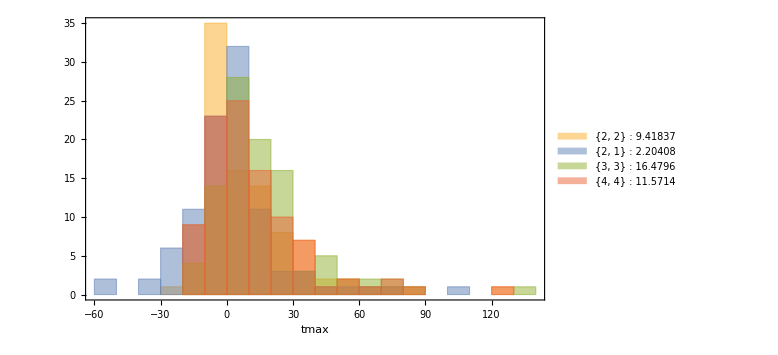

```mathematica
Histogram[tdifss,Frame->True,FrameLabel->{"tmax"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes[[i]]]<>" : "<>leg[[i]],{i,Length@modes}],{0.85,0.8}]]
```

```mathematica
wvcomban=Table[WaveCombine[sxsrhsv1[[i,{1,3,4}]],modes[[{1,3,4}]],2.3,0,False],{i,Length@sxsrhsv1}];
```

```mathematica
tmaxan=Table[TimeOfMaximum[wvcomban[[i]][[Round[(Length@wvcomban[[i]])/2] ;; -1]]],{i,Length@wvcomban}];
tdifss=Table[TimeOfMaximum[sxsrhsv1[[i,{1,3,4}]][[index]][[Round[(Length@sxsrhsv1[[i,{1,3,4}]][[index]])/2] ;; -1]]]-tmaxan[[i]],{index,3},{i,Length@wvcomban}];
```

```mathematica
leg=ToString/@Mean/@tdifss
st=ToString/@StandardDeviation/@tdifss
```

{1.81122,8.87245,3.96429}

{8.86802,10.9806,8.96075}

{{2,2},{3,3},{4,4}}

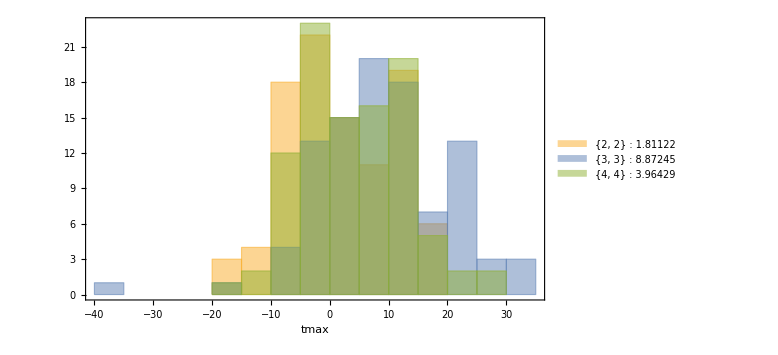

```mathematica
modes2={{2,2},{3,3},{4,4}}
Histogram[tdifss,Frame->True,FrameLabel->{"tmax"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes2[[i]]]<>" : "<>leg[[i]],{i,3}],{0.15,0.8}]]
```

{-0.000107785,0.0113672}

{0.0134987,0.0163598}

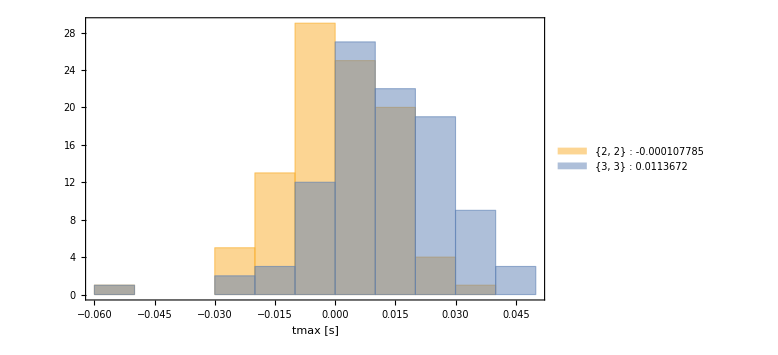

```mathematica
wvcomban=Table[WaveCombine[sxsrhsv1[[i,{1,3}]],modes[[{1,3}]],2.3,0,False],{i,Length@sxsrhsv1}];
tmaxan=Table[TimeOfMaximum[wvcomban[[i]][[Round[(Length@wvcomban[[i]])/2] ;; -1]]],{i,Length@wvcomban}];
tdifss=Table[tPhys[TimeOfMaximum[sxsrhsv1[[i,{1,3}]][[index]][[Round[(Length@sxsrhsv1[[i,{1,3}]][[index]])/2] ;; -1]]]-tmaxan[[i]],330],{index,2},{i,Length@wvcomban}];
leg=ToString/@Mean/@tdifss
st=ToString/@StandardDeviation/@tdifss
Histogram[tdifss,8,Frame->True,FrameLabel->{"tmax [s]"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes2[[i]]]<>" : "<>leg[[i]],{i,2}],{0.8,0.8}]]
```

```mathematica
Length@tdifss
```

2

{-0.0663265,6.9949}

{8.30651,10.0672}

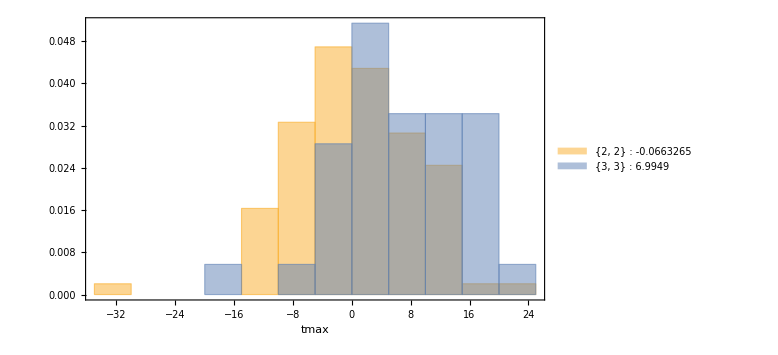

```mathematica
wvcomban=Table[WaveCombine[sxsrhsv1[[i,{1,3}]],modes[[{1,3}]],2.3,0,False],{i,Length@sxsrhsv1}];
tmaxan=Table[TimeOfMaximum[wvcomban[[i]][[Round[(Length@wvcomban[[i]])/2] ;; -1]]],{i,Length@wvcomban}];
tdifss=Table[TimeOfMaximum[sxsrhsv1[[i,{1,3}]][[index]][[Round[(Length@sxsrhsv1[[i,{1,3}]][[index]])/2] ;; -1]]]-tmaxan[[i]],{index,2},{i,Length@wvcomban}];
leg=ToString/@Mean/@tdifss
st=ToString/@StandardDeviation/@tdifss
Histogram[{tdifss[[1]],tdifss[[2]][[pos]]},14,"PDF",Frame->True,FrameLabel->{"tmax "},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes2[[i]]]<>" : "<>leg[[i]],{i,2}],{0.8,0.8}]]
```

```mathematica
Median@tdifss[[2,pos]]
```

6.5

### q=2, χ=0.8, χeff~0.1

```mathematica
join=False;
sxsdir="/Users/xisco/mount/Atlas/SXS/data";
sxsdirs=Select[FileNames["*",sxsdir],DirectoryQ[#]&];
```

```mathematica
posl300=Flatten@Position[ToExpression[(StringSplit[#,"_"]&/@sxsdirs)[[All,-1]]],_?(#>=300&)];
sxsdirsl300=sxsdirs[[posl300]];
sxsdirsl300=sxsdirs;
```

```mathematica
mysxscase=SXSParClassification[sxsdirsl300,{{"MassRatio","1.3<#<2.5"},{"Final-Spin","0.8<#<0.9"},{"eccentricity","#<0.01"}},"Verbose"->True,"MetadataType"->"json","Mass1-Str"->"reference-mass1","Mass2-Str"->"reference-mass2"]
(*mysxscase=SXSParClassification[sxsdirsl300,{{"Non-Precessing"},{"MassRatio","1.9<#<2.5"},{"χ1","#<0.5"},{"χ2","#<0.5"},{"eccentricity","#<0.01"},{"Final-Spin","0.8<#<0.9"}},"Verbose"->True,"MetadataType"->"json"]*)
(*mysxscase=SXSParClassification[sxsdirsl300,{{"eccentricity","#<0.01"},{"MassRatio","1.2<#<2.5"},{"Final-Spin","0.8<#<0.9"}},"Verbose"->True,"MetadataType"->"json"]*)
modes={{2,2},{2,1},{3,3},{4,4}}
```

Classification Input Variables. Examples: {{'MassRatio', '0.99<#<1.1'}},{{'Distance', '#>16'}},{{'Orbits', '#>25'}},{{'Precessing'}},
{{'CBCType','BHBH'},{'Non-Precessing'}},{{'High-Spin'}},{{'χeff','#>0.6'}},{{'χ1','#>0.6'}},{{'χ2','#>0.6'}},{{'Unequal'}}

Take care! Some of the sxs file names are not consistent with the metadata files

The spin definition is consitent with 'initial-spin' values and not relaxed ones

The mass definition is consitent with 'initial-mass' values and not relaxed ones

PreDecrement::rvalue: -50000 is not a variable with a value, so its value cannot be changed.

PreDecrement::rvalue: --(-50000) is not a variable with a value, so its value cannot be changed.

Case | q | χ1 | χ2 | D | e | simulation name
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0652 | 1.3 | {-0.05, -0.02, 0.8} | {0.42, -0.68, 0.} | initial-separation | 0.0005894 | 0019/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0653 | 1.3 | {0., 0.05, 0.8} | {-0.8, -0.02, 0.} | initial-separation | 0.0001174 | 0020/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0654 | 1.3 | {0.05, -0.03, 0.8} | {0.38, 0.7, 0.} | initial-separation | 0.0007237 | 0021/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1064 | 1.3 | {-0.16, -0.69, 0.19} | {0.23, -0.58, 0.44} | initial-separation | 0.0006 | 1071/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0588 | 1.4 | {0., 0.11, 0.79} | {0., 0., 0.64} | initial-separation | 0.000173 | 0286/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1032 | 1.4 | {0.51, 0.26, 0.5} | {0.06, 0.55, 0.27} | initial-separation | 0.0002725 | 1038/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1072 | 1.4 | {-0.08, -0.7, 0.35} | {-0.67, -0.07, 0.22} | initial-separation | 0.0005093 | 1079/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1413 | 1.4 | {0., 0., 0.5} | {0., 0., 0.4} | initial-separation | 0.0019 | 002/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0372 | 1.5 | {0., 0., 0.8} | {0., 0., -0.4} | initial-separation | 0.0005048 | 0050/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0380 | 1.5 | {0., 0.56, 0.57} | {0.06, 0., 0.8} | initial-separation | 0.0006321 | 0058/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0385 | 1.5 | {0., 0., 0.8} | {0., 0., 0.} | initial-separation | 0.0002454 | 0064/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0441 | 1.5 | {0., 0., 0.6} | {0., 0., 0.8} | initial-separation | 0.0003625 | 0125/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0526 | 1.5 | {0.04, 0.43, 0.29} | {0.04, -0.01, 0.79} | initial-separation | 0.0003189 | 0221/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1011 | 1.5 | {0.61, 0.06, 0.28} | {0.59, 0.19, 0.43} | initial-separation | 0.00057 | 1017/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1415 | 1.5 | {0., 0., 0.5} | {0., 0., 0.5} | initial-separation | 0.00048 | 004/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1473 | 1.5 | {0., 0., 0.7} | {0., 0., 0.79} | initial-separation | 0.0004604 | 063/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0519 | 1.6 | {0., 0., 0.64} | {0., 0., 0.41} | initial-separation | 0.0004125 | 0214/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1090 | 1.6 | {-0.43, -0.17, 0.46} | {-0.48, -0.09, 0.48} | initial-separation | 0.00034 | 1097/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0388 | 1.7 | {0., 0., 0.8} | {0., 0., 0.4} | initial-separation | 0.0008282 | 0067/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0435 | 1.7 | {0., 0., 0.4} | {0., 0., 0.8} | initial-separation | 0.000266 | 0118/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0531 | 1.7 | {-0.07, 0.55, 0.57} | {0.07, 0., 0.8} | initial-separation | 0.0002 | 0226/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0552 | 1.7 | {0., 0., 0.8} | {0., 0., -0.4} | initial-separation | 0.0004337 | 0250/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0581 | 1.7 | {0.07, 0.6, 0.47} | {0., 0., 0.07} | initial-separation | 0.0003082 | 0279/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0679 | 1.7 | {-0.04, -0.03, 0.8} | {0.49, -0.63, 0.} | initial-separation | 0.0004666 | 0046/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0680 | 1.7 | {0., 0.05, 0.8} | {-0.79, -0.11, 0.} | initial-separation | 0.0005332 | 0047/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0681 | 1.7 | {0.05, -0.02, 0.8} | {0.3, 0.74, 0.} | initial-separation | 0.0005557 | 0048/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1014 | 1.7 | {-0.54, 0.39, 0.3} | {-0.38, 0.43, 0.43} | initial-separation | 0.00072 | 1020/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0496 | 1.8 | {-0.03, 0.17, 0.76} | {0.02, 0., 0.75} | initial-separation | 0.000346 | 0188/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0501 | 1.8 | {0., 0., 0.6} | {0., 0., 0.8} | initial-separation | 0.0004158 | 0194/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1054 | 1.8 | {0.45, 0.32, 0.52} | {0.56, -0.31, -0.17} | initial-separation | 0.0006768 | 1060/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1058 | 1.8 | {0.08, -0.48, 0.44} | {0.09, 0.65, 0.42} | initial-separation | 0.0004909 | 1065/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1084 | 1.8 | {0.35, -0.37, 0.48} | {-0.47, 0.57, 0.31} | initial-separation | 0.0004235 | 1091/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0497 | 1.9 | {-0.07, 0.64, 0.47} | {0.06, 0., 0.65} | initial-separation | 0.0005561 | 0189/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1469 | 1.9 | {0., 0., 0.8} | {0., 0., 0.67} | initial-separation | 0.0001015 | 059/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0162 | 2. | {0., 0., 0.6} | {0., 0., 0.} | initial-separation | 0.0063771 | d13.9_q2.00_sA_0.000_0.000_0.600_sB_0.000_0.000_0.000/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0253 | 2. | {0., 0., 0.5} | {0., 0., 0.5} | initial-separation | 0.00062 | BBH_CFMS_d16.4_q2_sA_0_0_0.500_sB_0_0_0.500/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0255 | 2. | {0., 0., 0.6} | {0., 0., 0.} | initial-separation | 0.0001873 | BBH_SKS_d15.2_q2_sA_0_0_0.600_sB_0_0_0/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0256 | 2. | {0., 0., 0.6} | {0., 0., 0.6} | initial-separation | 0.0001176 | BBH_SKS_d15_q2_sA_0_0_0.600_sB_0_0_0.600/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0258 | 2. | {0., 0., 0.87} | {0., 0., -0.85} | initial-separation | 0.0002479 | BBH_SKS_d15.2_q2_sA_0_0_0.871_sB_0_0_-0.850/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0374 | 2. | {-0.04, 0.56, 0.57} | {0., 0., 0.} | initial-separation | 0.00019 | 0052/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0379 | 2. | {-0.08, 0.41, 0.43} | {0.05, 0., 0.8} | initial-separation | 0.0000802 | 0057/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0410 | 2. | {0., 0., 0.6} | {0., 0., 0.} | initial-separation | 0.000429 | 0089/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0425 | 2. | {-0.09, 0.55, 0.57} | {0.04, 0., 0.4} | initial-separation | 0.0001901 | 0106/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0427 | 2. | {0., 0.56, 0.57} | {-0.03, 0., -0.4} | initial-separation | 0.0001817 | 0108/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0453 | 2. | {-0.03, 0.42, 0.5} | {0.01, 0., 0.21} | initial-separation | 0.0004945 | 0141/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0592 | 2. | {-0.03, 0.15, 0.72} | {0., 0., 0.36} | initial-separation | 0.0002523 | 0291/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0705 | 2. | {-0.03, -0.03, 0.8} | {0.57, -0.56, 0.} | initial-separation | 0.00013 | 0073/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0706 | 2. | {-0.01, 0.04, 0.8} | {-0.77, -0.22, 0.} | initial-separation | 0.0005397 | 0074/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0707 | 2. | {0.05, -0.01, 0.8} | {0.2, 0.78, 0.} | initial-separation | 0.0003353 | 0075/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0745 | 2. | {-0.37, -0.42, 0.57} | {0., 0., 0.} | initial-separation | 0.0002443 | 0121/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0747 | 2. | {-0.29, -0.48, 0.57} | {-0.05, 0.04, 0.8} | initial-separation | 0.00019 | 0123/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0748 | 2. | {-0.4, -0.44, 0.54} | {0.5, -0.62, 0.07} | initial-separation | 0.0001817 | 0124/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0749 | 2. | {-0.34, -0.43, 0.58} | {0.3, 0.74, -0.02} | initial-separation | 0.0004145 | 0126/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0751 | 2. | {-0.2, 0.51, 0.58} | {0.49, -0.63, -0.03} | initial-separation | 0.0002383 | 0128/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0752 | 2. | {-0.19, 0.56, 0.54} | {-0.79, -0.12, 0.07} | initial-separation | 0.000448 | 0129/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0754 | 2. | {0.55, -0.1, 0.57} | {0., 0., 0.} | initial-separation | 0.0001625 | 0132/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0756 | 2. | {0.56, 0., 0.57} | {-0.01, -0.06, 0.8} | initial-separation | 0.00022 | 0134/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0757 | 2. | {0.55, -0.08, 0.58} | {-0.79, -0.11, -0.03} | initial-separation | 0.00025 | 0136/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0758 | 2. | {0.58, -0.11, 0.53} | {0.29, 0.74, 0.07} | initial-separation | 0.00018 | 0137/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0759 | 2. | {0.53, -0.2, 0.57} | {0.03, 0.05, -0.8} | initial-separation | 0.00021 | 0138/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0852 | 2. | {-0.02, -0.01, 0.8} | {0.29, -0.28, 0.} | initial-separation | 0.000262 | 0234/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0860 | 2. | {0., 0.02, 0.8} | {-0.39, -0.11, 0.} | initial-separation | 0.0000839 | 0245/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0871 | 2. | {0.02, 0., 0.8} | {0.1, 0.39, 0.} | initial-separation | 0.0006206 | 0256/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0894 | 2. | {0.03, 0., 0.8} | {-0.2, 0.52, 0.57} | initial-separation | 0.0003431 | 0282/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0904 | 2. | {0., -0.03, 0.8} | {0.56, -0.08, 0.57} | initial-separation | 0.0001793 | 0292/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0914 | 2. | {-0.04, 0.03, 0.8} | {-0.56, -0.58, 0.} | initial-separation | 0.0003308 | 0302/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0922 | 2. | {0.05, 0., 0.8} | {-0.22, 0.77, 0.} | initial-separation | 0.0002727 | 0310/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0932 | 2. | {-0.01, -0.04, 0.8} | {0.78, -0.19, 0.} | initial-separation | 0.0002872 | 0320/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0941 | 2. | {-0.02, 0.03, 0.8} | {-0.43, -0.37, -0.56} | initial-separation | 0.0001133 | 0329/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0948 | 2. | {0.03, 0., 0.8} | {-0.11, 0.56, -0.56} | initial-separation | 0.0006267 | 0336/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0955 | 2. | {-0.01, -0.03, 0.8} | {0.54, -0.19, -0.56} | initial-separation | 0.000077 | 0343/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0962 | 2. | {0.03, 0.03, 0.8} | {-0.56, 0.57, 0.} | initial-separation | 0.0001032 | 0350/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0972 | 2. | {0.04, -0.03, 0.8} | {0.57, 0.56, 0.} | initial-separation | 0.0003106 | 0360/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0980 | 2. | {-0.03, -0.03, 0.8} | {0.56, -0.57, 0.} | initial-separation | 0.0006403 | 0369/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0988 | 2. | {-0.04, 0.03, 0.8} | {-0.57, -0.56, 0.} | initial-separation | 0.0005057 | 0377/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1087 | 2. | {0.3, 0.48, 0.47} | {-0.38, -0.47, 0.35} | initial-separation | 0.0001701 | 1094/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1209 | 2. | {0.06, -0.01, 0.85} | {0.18, 0.83, 0.} | initial-separation | 0.0006064 | 0036/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1478 | 2. | {0., 0., 0.8} | {0., 0., 0.13} | initial-separation | 0.0010752 | 068/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1800 | 2. | {0.54, -0.26, 0.49} | {0.38, -0.57, 0.11} | initial-separation | 0.00048 | 0313/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1846 | 2. | {-0.25, -0.3, 0.61} | {-0.64, 0.23, 0.37} | initial-separation | 0.00042 | 0360/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2127 | 2. | {0., 0., 0.5} | {0., 0., 0.5} | initial-separation | 0.0002818 | 0253/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2129 | 2. | {0., 0., 0.6} | {0., 0., 0.} | initial-separation | 0.0006143 | 0255/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2130 | 2. | {0., 0., 0.6} | {0., 0., 0.6} | initial-separation | 0.0003712 | 0256/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2132 | 2. | {0., 0., 0.87} | {0., 0., -0.85} | initial-separation | 0.0002126 | 0258/Lev2
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1877 | 2.1 | {-0.48, -0.03, 0.61} | {0.33, 0.3, -0.06} | initial-separation | 0.0006399 | 0391/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1716 | 2.2 | {-0.21, 0.42, 0.53} | {-0.56, 0.18, 0.42} | initial-separation | 0.000373 | 0225/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1841 | 2.2 | {-0.23, 0.21, 0.58} | {0.35, -0.32, 0.48} | initial-separation | 0.0002789 | 0355/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1459 | 2.3 | {0., 0., 0.76} | {0., 0., 0.8} | initial-separation | 0.001533 | 049/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1468 | 2.3 | {0., 0., 0.51} | {0., 0., 0.8} | initial-separation | 0.0009304 | 058/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1645 | 2.3 | {-0.42, -0.3, 0.44} | {-0.33, -0.56, 0.43} | initial-separation | 0.0006655 | 0153/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1664 | 2.3 | {0.43, -0.35, 0.51} | {0.46, 0.11, 0.} | initial-separation | 0.00014 | 0172/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1718 | 2.3 | {-0.19, 0.42, 0.6} | {0.11, 0.73, -0.12} | initial-separation | 0.0006176 | 0227/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1775 | 2.3 | {0.31, 0.52, 0.5} | {0.02, 0.43, 0.21} | initial-separation | 0.00033 | 0286/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1453 | 2.4 | {0., 0., 0.8} | {0., 0., -0.78} | initial-separation | 0.0004626 | 043/Lev1
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1638 | 2.4 | {-0.58, -0.05, 0.51} | {0., -0.55, -0.34} | initial-separation | 0.0001438 | 0146/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1763 | 2.4 | {0.39, -0.26, 0.58} | {-0.32, -0.53, 0.18} | initial-separation | 0.000311 | 0274/Lev3
/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1685 | 2.5 | {-0.34, 0.53, 0.5} | {0.6, 0.36, 0.21} | initial-separation | 0.00065 | 0193/Lev3

{/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0652,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0653,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0654,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1064,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0588,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1032,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1072,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1413,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0372,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0380,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0385,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0441,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0526,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1011,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1415,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1473,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0519,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1090,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0388,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0435,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0531,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0552,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0581,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0679,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0680,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0681,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1014,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0496,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0501,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1054,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1058,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1084,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0497,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1469,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0162,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0253,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0255,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0256,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0258,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0374,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0379,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0410,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0425,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0427,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0453,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0592,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0705,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0706,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0707,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0745,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0747,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0748,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0749,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0751,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0752,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0754,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0756,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0757,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0758,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0759,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0852,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0860,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0871,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0894,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0904,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0914,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0922,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0932,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0941,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0948,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0955,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0962,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0972,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0980,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0988,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1087,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1209,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1478,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1800,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1846,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2127,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2129,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2130,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2132,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1877,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1716,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1841,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1459,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1468,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1645,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1664,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1718,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1775,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1453,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1638,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1763,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1685}

{{2,2},{2,1},{3,3},{4,4}}

```mathematica
mysxscaserh=Table[FileNames["*rhO*",mysxscase[[i]],2][[-1]],{i,Length@mysxscase}]
(*mysxscasemetafile=Flatten[Table[FileNames["metadata.txt",FileNameDrop[mysxscaserh[[i]],-2],2][[-1]],{i,Length@mysxscaserh}]]*)
mysxscasemetafile=Flatten[Table[FileNames["metadata.json",FileNameDrop[mysxscaserh[[i]],-1],2][[-1]],{i,Length@mysxscaserh}]]
```

{/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0652/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0653/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0654/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1064/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0588/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1032/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1072/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1413/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0372/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0380/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0385/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0441/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0526/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1011/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1415/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1473/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0519/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1090/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0388/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0435/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0531/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0552/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0581/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0679/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0680/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0681/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1014/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0496/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0501/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1054/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1058/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1084/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0497/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1469/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0162/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0253/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0255/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0256/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0258/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0374/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0379/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0410/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0425/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0427/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0453/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0592/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0705/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0706/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0707/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0745/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0747/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0748/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0749/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0751/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0752/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0754/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0756/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0757/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0758/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0759/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0852/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0860/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0871/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0894/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0904/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0914/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0922/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0932/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0941/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0948/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0955/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0962/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0972/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0980/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0988/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1087/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1209/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1478/Lev1/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1800/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1846/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2127/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2129/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2130/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2132/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1877/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1716/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1841/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1459/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1468/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1645/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1664/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1718/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1775/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1453/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1638/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1763/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1685/rhOverM_Asymptotic_GeometricUnits_CoM.h5}

{/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0652/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0653/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0654/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1064/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0588/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1032/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1072/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1413/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0372/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0380/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0385/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0441/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0526/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1011/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1415/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1473/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0519/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1090/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0388/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0435/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0531/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0552/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0581/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0679/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0680/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0681/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1014/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0496/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0501/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1054/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1058/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1084/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0497/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1469/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0162/Lev4/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0253/Lev5/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0255/Lev5/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0256/Lev5/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0258/Lev5/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0374/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0379/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0410/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0425/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0427/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0453/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0592/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0705/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0706/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0707/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0745/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0747/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0748/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0749/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0751/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0752/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0754/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0756/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0757/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0758/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0759/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0852/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0860/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0871/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0894/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0904/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0914/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0922/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0932/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0941/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0948/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0955/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0962/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0972/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0980/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_0988/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1087/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1209/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1478/Lev1/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1800/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1846/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2127/Lev4/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2129/Lev4/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2130/Lev4/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_2132/Lev4/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1877/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1716/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1841/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1459/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1468/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1645/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1664/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1718/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1775/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1453/Lev3/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1638/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1763/metadata.json,/Users/xisco/mount/Atlas/SXS/data/SXS_BBH_1685/metadata.json}

```mathematica
(* For json *)
mysxscasemetadata=Import/@mysxscasemetafile;
altnames=("alternative_names"/.mysxscasemetadata);
altnames=Table[If[Length@altnames[[i]]≠ 0,altnames[[i]],{altnames[[i]]}],{i,Length@altnames}][[All,-1]];
Print["tag = ",tag=StringReplace[(altnames),":BBH"->""]]
Print["mass1 = ",mass1=Flatten[("initial_mass1"/.mysxscasemetadata),1]]
Print["mass2 = ",mass2=Flatten[("initial_mass2"/.mysxscasemetadata),1]]
Print["χ1 = ",χ1=Chop[(("initial_dimensionless_spin1"/.mysxscasemetadata)[[All,-1]])]]
Print["χ2 = ",χ2=Chop[(("initial_dimensionless_spin2"/.mysxscasemetadata)[[All,-1]])]]
Print["χeff = ",χeff=χ1*mass1+χ2*mass2]
Print["m1/m2 = ",q=mass1/mass2]
Print["m1·m2 = ",η=q/(1+q)^2*1.]
Print["af = ",af=Norm/@("remnant_dimensionless_spin"/.mysxscasemetadata)]
Print["mf = ",mf=("remnant_mass"/.mysxscasemetadata)]
Print["kick = ", vr=("remnant_velocity"/.mysxscasemetadata) ]
```

tag = {SXS:0652,SXS:0653,SXS:0654,SXS:1064,SXS:0588,SXS:1032,SXS:1072,SXS:1413,SXS:0372,SXS:0380,SXS:0385,SXS:0441,SXS:0526,SXS:1011,SXS:1415,SXS:1473,SXS:0519,SXS:1090,SXS:0388,SXS:0435,SXS:0531,SXS:0552,SXS:0581,SXS:0679,SXS:0680,SXS:0681,SXS:1014,SXS:0496,SXS:0501,SXS:1054,SXS:1058,SXS:1084,SXS:0497,SXS:1469,Case4a,SXS:0253,SXS:0255,SXS:0256,SXS:0258,SXS:0374,SXS:0379,SXS:0410,SXS:0425,SXS:0427,SXS:0453,SXS:0592,SXS:0705,SXS:0706,SXS:0707,SXS:0745,SXS:0747,SXS:0748,SXS:0749,SXS:0751,SXS:0752,SXS:0754,SXS:0756,SXS:0757,SXS:0758,SXS:0759,SXS:0852,SXS:0860,SXS:0871,SXS:0894,SXS:0904,SXS:0914,SXS:0922,SXS:0932,SXS:0941,SXS:0948,SXS:0955,SXS:0962,SXS:0972,SXS:0980,SXS:0988,SXS:1087,SXS:1209,SXS:1478,SXS:1800,SXS:1846,SXS:2127,SXS:2129,SXS:2130,SXS:2132,SXS:1877,SXS:1716,SXS:1841,SXS:1459,SXS:1468,SXS:1645,SXS:1664,SXS:1718,SXS:1775,SXS:1453,SXS:1638,SXS:1763,SXS:1685}

mass1 = {0.571429,0.571429,0.571429,0.570046,0.586469,0.588586,0.58698,0.585062,0.6,0.6,0.6,0.6,0.593798,0.604533,0.6,0.591867,0.610208,0.613619,0.636364,0.636364,0.636364,0.636364,0.626663,0.625,0.625,0.625,0.628586,0.636411,0.636364,0.645175,0.644925,0.638104,0.650739,0.649254,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.664828,0.666223,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.666667,0.662027,0.666667,0.663599,0.668106,0.668448,0.666667,0.666667,0.666667,0.666667,0.679492,0.690942,0.689245,0.693205,0.694033,0.695727,0.699415,0.698093,0.695672,0.701728,0.706525,0.705047,0.71247}

mass2 = {0.428571,0.428571,0.428571,0.429954,0.413531,0.411414,0.41302,0.414938,0.4,0.4,0.4,0.4,0.406202,0.395467,0.4,0.408133,0.389792,0.386381,0.363636,0.363636,0.363636,0.363636,0.373337,0.375,0.375,0.375,0.371414,0.363589,0.363636,0.354825,0.355075,0.361896,0.349261,0.350746,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.335172,0.333777,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.333333,0.337973,0.333333,0.336401,0.331894,0.331552,0.333333,0.333333,0.333333,0.333333,0.320508,0.309058,0.310755,0.306795,0.305967,0.304273,0.300585,0.301907,0.304328,0.298272,0.293475,0.294953,0.28753}

χ1 = {0.798133,0.798168,0.79785,0.19429,0.789871,0.502441,0.349256,0.5,0.8,0.571628,0.8,0.6,0.293471,0.282484,0.5,0.697636,0.638641,0.464707,0.8,0.4,0.57278,0.8,0.473937,0.798489,0.798473,0.798191,0.299999,0.76462,0.6,0.523373,0.440777,0.475158,0.467288,0.8,0.6,0.5,0.6,0.6,0.871346,0.571719,0.428682,0.6,0.572863,0.57061,0.498706,0.724539,0.798729,0.798675,0.798428,0.566595,0.568408,0.535453,0.577058,0.580711,0.541181,0.56917,0.570095,0.580359,0.534523,0.568265,0.799682,0.799669,0.799607,0.799232,0.79936,0.798491,0.798547,0.798793,0.799298,0.799316,0.799432,0.798723,0.798498,0.798723,0.798498,0.468263,0.84809,0.8,0.485579,0.609633,0.5,0.6,0.6,0.871346,0.614571,0.529036,0.580405,0.763217,0.514713,0.442388,0.505058,0.595923,0.498169,0.8,0.513841,0.577596,0.495911}

χ2 = {0.0080225,0.00460341,0.00533492,0.443994,0.641976,0.266228,0.217381,0.4,-0.4,0.797652,-4.47696×10^-8,0.8,0.787363,0.432761,0.5,0.787879,0.412651,0.484742,0.4,0.8,0.797195,-0.4,0.0719241,0.00814238,0.00521626,0.00565526,0.430569,0.754935,0.8,-0.169461,0.417501,0.307281,0.645002,0.668909,-3.08393×10^-8,0.5,-1.09515×10^-8,0.6,-0.85,-1.24778×10^-7,0.798229,-3.93804×10^-8,0.398415,-0.398536,0.211338,0.362423,0.00853558,0.00573377,0.00612983,-7.76057×10^-8,0.796993,0.0730079,-0.024054,-0.0278831,0.0741505,-1.87813×10^-7,0.797386,-0.0275043,0.0675596,-0.797639,0.00212898,0.00143109,0.00152807,0.570103,0.56971,0.00506595,0.00787645,0.00745676,-0.563396,-0.562213,-0.562268,0.00854321,0.00505644,0.00854321,0.00505643,0.348705,0.00735338,0.126264,0.108436,0.36886,0.5,-2.84598×10^-8,0.6,-0.85,-0.0572666,0.423889,0.479955,0.8,0.8,0.434385,0.00538853,-0.117041,0.206831,-0.784548,-0.338092,0.178799,0.206435}

χeff = {0.459514,0.458069,0.458201,0.301651,0.728712,0.405259,0.294789,0.458506,0.32,0.662038,0.48,0.68,0.494091,0.341914,0.5,0.734467,0.550552,0.472448,0.654545,0.545455,0.654386,0.363636,0.32385,0.502109,0.501002,0.50099,0.348494,0.761098,0.672727,0.277538,0.432512,0.414403,0.529356,0.75402,0.4,0.5,0.4,0.6,0.297564,0.381146,0.551865,0.4,0.514714,0.247561,0.402389,0.603673,0.535331,0.534361,0.534328,0.37773,0.644603,0.381305,0.376688,0.377847,0.385504,0.379447,0.645859,0.377738,0.378869,0.112964,0.533831,0.53359,0.533581,0.722856,0.72281,0.534016,0.53499,0.535014,0.345067,0.345473,0.345532,0.53533,0.534017,0.53533,0.534017,0.427855,0.567845,0.573354,0.360407,0.529804,0.5,0.4,0.6,0.297564,0.399242,0.496539,0.54919,0.774502,0.602002,0.439953,0.354865,0.380674,0.409507,0.327373,0.26382,0.459969,0.412678}

m1/m2 = {1.33333,1.33333,1.33333,1.32583,1.4182,1.43064,1.42119,1.41,1.5,1.5,1.5,1.5,1.46183,1.52865,1.5,1.45018,1.56547,1.58812,1.75,1.75,1.75,1.75,1.67854,1.66667,1.66667,1.66667,1.69241,1.75036,1.75,1.81829,1.81631,1.76322,1.86319,1.85107,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,1.98355,1.99601,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,1.95881,2.,1.97264,2.01301,2.01612,2.,2.,2.,2.,2.12005,2.23564,2.21796,2.25951,2.26833,2.28653,2.32685,2.31228,2.28593,2.35264,2.40744,2.39037,2.4779}

m1·m2 = {0.244898,0.244898,0.244898,0.245094,0.242523,0.242152,0.242434,0.242764,0.24,0.24,0.24,0.24,0.241202,0.239073,0.24,0.24156,0.237854,0.237091,0.231405,0.231405,0.231405,0.231405,0.233957,0.234375,0.234375,0.234375,0.233466,0.231392,0.231405,0.228924,0.228997,0.230927,0.227278,0.227723,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222832,0.22237,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.222222,0.223747,0.222222,0.223235,0.22174,0.221625,0.222222,0.222222,0.222222,0.222222,0.217783,0.213541,0.214187,0.212672,0.212351,0.211691,0.210234,0.210759,0.211713,0.209306,0.207348,0.207956,0.204856}

af = {0.856771,0.848846,0.855866,0.801361,0.893084,0.825287,0.803796,0.815925,0.814922,0.868309,0.847339,0.8656,0.808083,0.800959,0.821909,0.885821,0.844861,0.830187,0.882193,0.806429,0.869894,0.832926,0.807051,0.864578,0.871954,0.869825,0.80533,0.895107,0.856798,0.812521,0.802414,0.802416,0.835862,0.897235,0.80823,0.804636,0.808206,0.838563,0.841633,0.830992,0.8141,0.808243,0.845819,0.818211,0.806759,0.864112,0.876377,0.876811,0.871447,0.83126,0.861802,0.83968,0.816842,0.8205,0.842811,0.82775,0.866295,0.816743,0.831767,0.802625,0.869614,0.869345,0.867427,0.895907,0.894589,0.872892,0.872789,0.877895,0.849404,0.842105,0.851056,0.875682,0.873204,0.875632,0.87336,0.804306,0.88848,0.870766,0.82209,0.845609,0.804772,0.808199,0.838578,0.841638,0.83076,0.835859,0.82691,0.889665,0.811883,0.817505,0.820368,0.829313,0.834352,0.84061,0.810422,0.834653,0.832303}

mf = {0.933603,0.929708,0.932964,0.939345,0.920163,0.936271,0.94046,0.937731,0.940575,0.924424,0.934287,0.927516,0.937027,0.940854,0.937224,0.921928,0.934269,0.937303,0.928766,0.940755,0.931349,0.94083,0.943369,0.930803,0.934344,0.934192,0.943096,0.923391,0.932327,0.945053,0.943709,0.9417,0.936771,0.924896,0.946062,0.945296,0.946063,0.939592,0.943737,0.944461,0.942913,0.945965,0.939132,0.949094,0.946391,0.936182,0.936376,0.937422,0.934249,0.945008,0.93397,0.944525,0.943064,0.944672,0.945083,0.942997,0.935539,0.943479,0.941565,0.951919,0.937258,0.937407,0.936365,0.928875,0.928332,0.935454,0.934636,0.937453,0.944631,0.941026,0.944414,0.935974,0.935665,0.935939,0.935742,0.942902,0.932685,0.935449,0.944034,0.939717,0.944804,0.946086,0.939612,0.943767,0.945256,0.944913,0.943984,0.932143,0.945573,0.948768,0.949871,0.946804,0.947474,0.947748,0.951507,0.948293,0.951737}

kick = {{-0.00036068,0.000433545,-0.00135791},{0.000347208,-0.000118486,-0.00364418},{0.000326426,0.000673053,0.00438503},{-0.000225672,0.00160883,-0.00501564},{0.0000767085,0.000029743,0.00178401},{-0.00061334,-0.00107028,-0.00493377},{0.000119424,0.000472662,-0.00502988},{-0.0000133136,0.0000974451,3.26112×10^-9},{-0.000393588,-0.000392111,1.26996×10^-8},{0.000126325,0.000801548,0.00699774},{0.00011198,0.000286558,-3.18846×10^-8},{0.0000969617,0.0000622846,2.89345×10^-8},{-0.000103815,-0.000113856,-0.00348401},{-0.000710355,-0.000386286,-0.00235895},{-0.000115448,-0.0000340461,-1.63656×10^-8},{8.75858×10^-6,0.0000430346,-1.8721×10^-8},{-0.000100166,-0.0000114181,-0.0000577446},{-0.000548419,-0.0000303585,0.00285253},{0.000131127,0.0000598274,3.3961×10^-8},{0.0000671339,-0.000269798,1.9336×10^-8},{-0.000240267,0.000576741,0.00341402},{0.00039588,0.000232898,3.58852×10^-8},{-0.000026832,0.000598003,0.00462989},{0.0000456538,-0.000157429,-0.000618175},{-0.000346669,-0.0000595189,0.00317557},{-0.000162874,-0.000288769,-0.00146363},{-0.00148548,0.000965756,0.00660998},{-0.0000416693,-0.000152471,-0.00291426},{-0.000038287,0.000112148,-9.89577×10^-9},{0.0000283962,-0.000108552,-0.0024452},{0.000191605,-0.000415189,0.00326781},{0.000615954,0.000361935,0.00803177},{-0.000224592,0.000904498,0.0072177},{-0.0000522588,-0.0000140389,7.24772×10^-8},{0.0000770303,0.00020595,9.17274×10^-9},{-0.000164891,-0.0000909748,1.18516×10^-8},{0.000123628,-0.000147649,-5.20424×10^-9},{-0.0000643764,-0.0000828048,-8.72426×10^-9},{-0.000300544,0.000492876,-4.82393×10^-9},{0.0000400425,-0.000509978,-0.00357773},{-0.0000176233,0.000531073,0.00342477},{-0.000190603,0.000116024,-5.4932×10^-8},{-0.000174515,0.000859982,0.00646169},{0.0000448333,0.000206643,0.00017369},{-0.0000279564,-0.000341886,-0.00202191},{0.0000159467,0.00013877,-0.000170134},{0.000040565,-0.0000667673,0.00120089},{0.000330948,0.0000105773,-0.00154456},{0.000071015,0.000334057,0.000447181},{-0.000130883,-0.000133151,-0.00023661},{-0.000510859,-0.000835235,0.00717446},{0.0000579152,0.000691695,-0.00448406},{-0.000194238,0.00030327,-0.0056908},{0.000017735,-0.000188873,-0.00105831},{-0.000372976,0.0000470561,0.00264257},{0.000475152,-0.0000993251,0.00550406},{-0.000402238,-0.000231724,-0.00105853},{0.000371331,0.000434055,0.00792802},{0.000712939,0.0000529644,0.00331911},{0.000125856,-0.000179451,0.00112627},{0.00012774,0.0000780047,0.000453043},{0.000138639,-0.0000288417,0.000855248},{0.000222588,0.0000571673,-0.00137164},{-0.0000467011,0.0000460343,0.000926811},{-0.000184896,-0.0000753554,-0.00234226},{0.000297698,0.000232094,-0.0010785},{-0.0000498274,0.000181059,-0.000232497},{0.000191638,-0.000107148,0.00156609},{0.000216035,0.000274507,-0.00244028},{-0.000451229,0.000276796,0.00272255},{9.0228×10^-6,-0.000225628,0.000267956},{0.0000108396,-0.000046085,-0.00100057},{0.000314493,0.000210847,0.0011347},{5.19793×10^-6,-0.0000294153,0.000989436},{0.000306701,0.000236538,-0.00115594},{-0.00031571,0.000667853,0.00664282},{0.00005866,0.000413874,0.00141052},{0.000165489,0.0000946411,1.66563×10^-7},{0.00113935,-0.000558602,0.00624831},{0.000306355,0.000103756,-0.00123859},{0.0000228334,-0.000192967,-4.22424×10^-8},{0.0000778914,-0.000202507,-2.54821×10^-8},{-0.0000676086,-0.000121886,-1.16576×10^-7},{-0.000325731,0.000443003,1.41171×10^-9},{0.00031376,-0.000119098,-0.00370891},{0.000331236,0.0000243807,-0.0021504},{-0.0000602859,0.000188803,-0.00105065},{8.62207×10^-6,0.0000836052,3.11739×10^-7},{-0.00020895,0.0000292832,1.37861×10^-7},{-0.000192727,-0.000593084,0.00323169},{-0.000526358,0.0000607948,-0.00356326},{-0.000213271,0.000254959,0.00324994},{0.00025233,0.000501026,0.00158396},{-0.0000916556,-0.000368515,-2.46084×10^-8},{0.000544366,0.000211989,-0.00338443},{-0.000499701,0.000272361,-0.00237064},{-0.000450571,0.000406761,0.00110794}}

```mathematica
modes={{2,2},{2,2},{3,3},{3,-3}}
```

{{2,2},{2,2},{3,3},{3,-3}}

```mathematica
sxsrhs=Conjugate/@GetAsymptoticMultiMode[#,2,modes,"ReSample"->True]&/@mysxscaserh;
```

$Aborted

```mathematica
tmax=TimeOfMaximum/@(sxsrhs[[All,1]])
```

{5089.14,4263.59,8328.41,6047.72,6036.2,5933.23,5095.15,5108.66,7961.68,6032.29,6035.78,5935.72,5094.62,5095.13,5088.12}

```mathematica
StandardDeviation[inclination]
```

0.301479

```mathematica
(* at 0 inclination*)
wvcomban=Table[WaveCombine[sxsrhs[[i]],modes,0,0,False],{i,Length@sxsrhs}];
tmaxan=Table[TimeOfMaximum[wvcomban[[i]][[Round[(Length@wvcomban[[i]])/2] ;; -1]]],{i,Length@wvcomban}];
tdifss=Table[TimeOfMaximum[sxsrhs[[i]][[index]][[Round[(Length@sxsrhs[[i]][[index]])/2] ;; -1]]]-tmaxan[[i]],{index,Length@modes},{i,Length@wvcomban}];
leg=ToString/@Mean/@tdifss
st=ToString/@StandardDeviation/@tdifss
Histogram[tdifss,14,"PDF",Frame->True,FrameLabel->{"tmax "},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes[[i]]]<>" : "<>leg[[i]],{i,Length@modes}],{0.8,0.8}]]
```

Infinity::indet: Indeterminate expression 0 ⅇ^(4 ⅈ p) √(7/π) ComplexInfinity encountered.

```mathematica
tdifss//TableForm
χeff
q
```

5089.14-NOMAX | 4263.59-NOMAX | 8328.41-NOMAX | 6047.72-NOMAX | 6036.2-NOMAX | 5933.23-NOMAX | 5095.15-NOMAX | 5108.66-NOMAX | 7961.68-NOMAX | 6032.29-NOMAX | 6035.78-NOMAX | 5935.72-NOMAX | 5094.62-NOMAX | 5095.13-NOMAX | 5088.12-NOMAX
5089.14-NOMAX | 4263.59-NOMAX | 8328.41-NOMAX | 6047.72-NOMAX | 6036.2-NOMAX | 5933.23-NOMAX | 5095.15-NOMAX | 5108.66-NOMAX | 7961.68-NOMAX | 6032.29-NOMAX | 6035.78-NOMAX | 5935.72-NOMAX | 5094.62-NOMAX | 5095.13-NOMAX | 5088.12-NOMAX
5096.64-NOMAX | 4268.59-NOMAX | 8334.41-NOMAX | 6053.72-NOMAX | 6043.2-NOMAX | 5938.23-NOMAX | 5100.65-NOMAX | 5114.66-NOMAX | 7967.68-NOMAX | 6037.79-NOMAX | 6042.28-NOMAX | 5941.22-NOMAX | 5101.62-NOMAX | 5101.13-NOMAX | 5093.62-NOMAX
5096.64-NOMAX | 4268.59-NOMAX | 8334.41-NOMAX | 6053.72-NOMAX | 6043.2-NOMAX | 5938.23-NOMAX | 5100.65-NOMAX | 5114.66-NOMAX | 7967.68-NOMAX | 6037.79-NOMAX | 6042.28-NOMAX | 5941.22-NOMAX | 5101.62-NOMAX | 5101.13-NOMAX | 5093.62-NOMAX
5090.14-NOMAX | 4264.59-NOMAX | 8328.91-NOMAX | 6048.72-NOMAX | 6036.7-NOMAX | 5935.23-NOMAX | 5096.15-NOMAX | 5109.66-NOMAX | 7962.18-NOMAX | 6033.29-NOMAX | 6036.78-NOMAX | 5938.22-NOMAX | 5095.12-NOMAX | 5095.13-NOMAX | 5090.12-NOMAX
5090.14-NOMAX | 4264.59-NOMAX | 8328.91-NOMAX | 6048.72-NOMAX | 6036.7-NOMAX | 5935.23-NOMAX | 5096.15-NOMAX | 5109.66-NOMAX | 7962.18-NOMAX | 6033.29-NOMAX | 6036.78-NOMAX | 5938.22-NOMAX | 5095.12-NOMAX | 5095.13-NOMAX | 5090.12-NOMAX
5085.14-NOMAX | 4262.59-NOMAX | 8331.91-NOMAX | 6040.22-NOMAX | 6037.7-NOMAX | 5942.73-NOMAX | 5092.15-NOMAX | 5077.16-NOMAX | 7965.68-NOMAX | 6029.79-NOMAX | 6038.78-NOMAX | 5945.22-NOMAX | 5095.62-NOMAX | 5099.13-NOMAX | 5098.62-NOMAX
5085.14-NOMAX | 4262.59-NOMAX | 8331.91-NOMAX | 6040.22-NOMAX | 6037.7-NOMAX | 5942.73-NOMAX | 5092.15-NOMAX | 5077.16-NOMAX | 7965.68-NOMAX | 6029.79-NOMAX | 6038.78-NOMAX | 5945.22-NOMAX | 5095.62-NOMAX | 5099.13-NOMAX | 5098.62-NOMAX

{0.75402,0.4,0.5,0.4,0.6,0.297564,0.4,0.573354,0.5,0.4,0.6,0.297564,0.774502,0.602002,0.327373}

{1.85107,2.,2.,2.,2.,2.,2.,1.97264,2.,2.,2.,2.,2.25951,2.26833,2.35264}

```mathematica
tNR[0.024,330]
```

14.7686

```mathematica
Dimensions@wvcomban
```

{15,9}

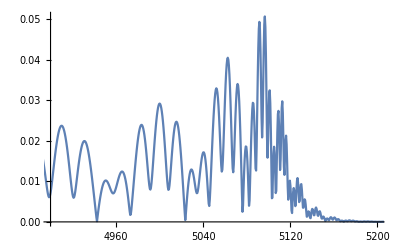

```mathematica
ListLinePlot[Abs0DStructs@wvcomban[[1,5]],PlotRange->{{4900,5200},All}]
```

{-3.53333,-3.53333,2.46667,2.46667}

{5.9174,5.9174,5.88262,5.88262}

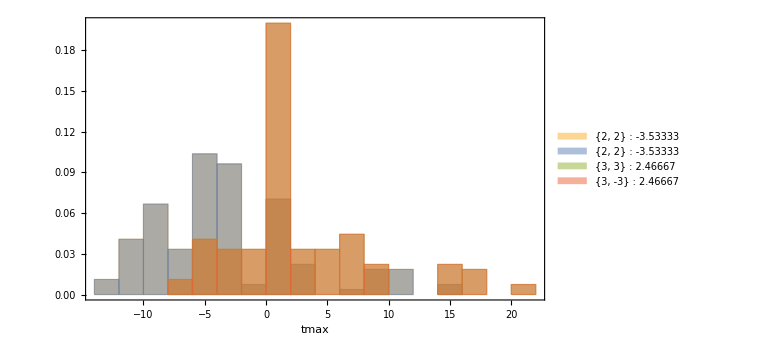

```mathematica
(* at 2.4+-0.3 inclination*)
wvcomban=Table[WaveCombine[sxsrhs[[i]],modes,2.4-0.3j,0,False],{i,Length@sxsrhs},{j,0,2,0.25}];
tmaxan=Table[TimeOfMaximum[wvcomban[[i,j]][[Round[(Length@wvcomban[[i,j]])/2] ;; -1]]],{i,Length@wvcomban},{j,Length[wvcomban[[i]]]}];
tdifss=Transpose[Flatten[Table[TimeOfMaximum[sxsrhs[[i]][[index]][[Round[(Length@sxsrhs[[i]][[index]])/2] ;; -1]]]-tmaxan[[i,j]],{j,9},{i,Length@wvcomban},{index,Length@modes}],1]];
tdifss22=Transpose[Flatten[Table[TimeOfMaximum[sxsrhs[[i]][[index]][[Round[(Length@sxsrhs[[i]][[index]])/2] ;; -1]]]-TimeOfMaximum[sxsrhs[[i]][[1]][[Round[(Length@sxsrhs[[i]][[1]])/2] ;; -1]]],{j,9},{i,Length@wvcomban},{index,Length@modes}],1]];
leg=ToString/@Mean/@tdifss
st=ToString/@StandardDeviation/@tdifss
Histogram[tdifss,14,"PDF",Frame->True,FrameLabel->{"tmax "},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes[[i]]]<>" : "<>leg[[i]],{i,Length@modes}],{0.8,0.8}]]
```

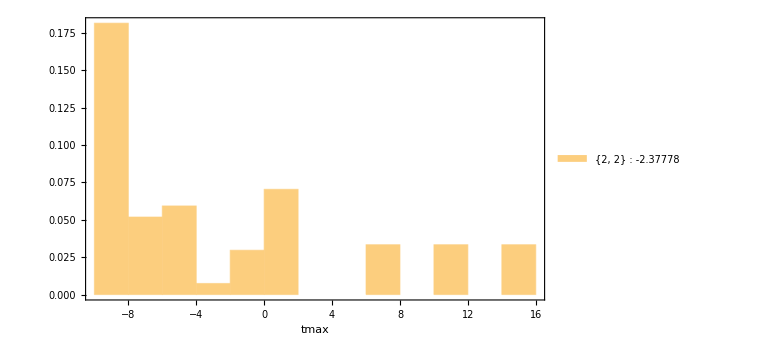

```mathematica
Histogram[tdifss[[1]],14,"PDF",Frame->True,FrameLabel->{"tmax "},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes[[i]]]<>" : "<>leg[[i]],{i,1}],{0.8,0.8}]]
```

```mathematica
q
```

{1.85107,2.,2.,2.,2.,2.,2.,1.97264,2.,2.,2.,2.,2.25951,2.26833,2.35264}

```mathematica
χeff
```

{0.75402,0.4,0.5,0.4,0.6,0.297564,0.4,0.573354,0.5,0.4,0.6,0.297564,0.774502,0.602002,0.327373}

```mathematica
10-tNR[0.007,330]
```

5.69249

```mathematica
tNR[0.007,330]
```

4.30751

```mathematica
tNR[0.024330,330]
tNR[0.0075,330]
```

14.9717

4.61519

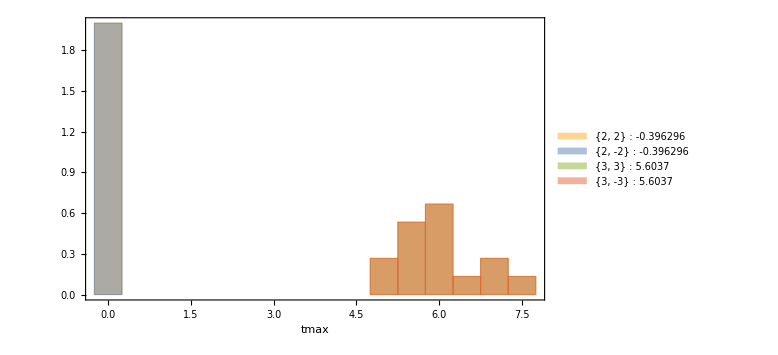

```mathematica
Histogram[tdifss22,14,"PDF",Frame->True,FrameLabel->{"tmax "},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full,ChartLegends->Placed[Table[ToString[modes[[i]]]<>" : "<>leg[[i]],{i,Length@modes}],{0.8,0.8}]]
```

```mathematica
FindRoot[{FinalSpinUIB2017[qq/(qq+1)^2,χχ,χχ]==0.85,a330[qq]==0.19},{qq,2,1,10},{χχ,0,-1,1}]
```

{qq→2.09778,χχ→0.641216}

```mathematica
FindRoot[{FinalSpinUIB2017[qq/(qq+1)^2,χχ,χχ]==0.85,a330[qq]==0.19},{qq,2,1,10},{χχ,0,-1,1}]
```

```mathematica
EradUIB2017[2.097782567363469/(2.09778256736346+1)^2,0.641,0.641]
```

0.0610957

```mathematica
Length@amp33
```

81683

```mathematica
qχ=Select[{qq,χχ}/.Table[FindRoot[{FinalSpinUIB2017[qq/(qq+1)^2,χχ,χχ]==finalspin[[i]],a330[qq]==amp33[[i]]},{qq,2,1,10},{χχ,0,-1,1}],{i,Length@amp33}],#[[1]]≠15&&-1≤ #[[2]]≤1&];
```

FindRoot::reged: The point {10.,0.667944} is at the edge of the search region {1.,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {10.,0.687263} is at the edge of the search region {1.,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {10.,0.73257} is at the edge of the search region {1.,10.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
qχdist=SmoothKernelDistribution[qχ]
```

DataDistribution[…]

```mathematica
h_{l|m|n}(t)&:=A_{lmn} X_{lmn}(\theta, \varphi)
e^{-t/\tau_{lmn}+i(2\pi f_{lmn}t+ \phi_{lmn})} \\
&+A_{l-mn} X_{l-mn}(\theta, \varphi)
e^{-t/\tau_{lmn}-i(2\pi f_{lmn}t+ \phi_{l-mn})}
```

```mathematica
??tNR
```

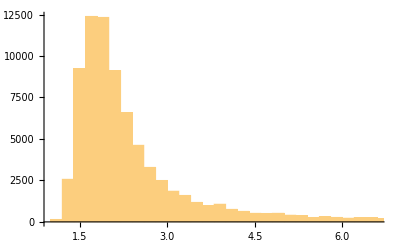

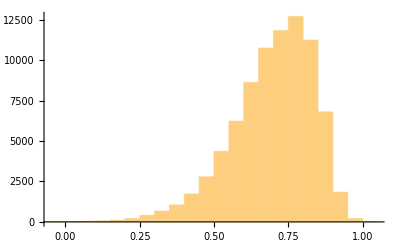

```mathematica
Histogram[qχ[[All,1]]]
Histogram[qχ[[All,2]]]
```

```mathematica
erad=EradUIB2017[qχ[[All,1]]/(qχ[[All,1]]+1)^2,qχ[[All,2]],qχ[[All,2]]]
```

{0.0197352,0.0729147,0.0806735,0.068138,0.05566,0.0156023,0.0160266,0.0709405,0.0740273,0.081682,0.0171525,0.0709237,0.0925713,0.0605966,0.0714621,0.066621,0.0206014,0.0669571,0.0788615,0.0613424,81644,0.0567112,0.0653966,0.0506392,0.0565043,0.0816037,0.0974073,0.0947503,0.0701664,0.0729117,0.0460276,0.0382677,0.0407651,0.0519065,0.0228679,0.0191559,0.0479672,0.0694887,0.0874415,0.0659393}
 |  |  |  |

```mathematica
1-156.3/163.9
```

0.0463697

```mathematica
q
```

{1.33333,1.33333,1.33333,1.32583,1.4182,1.43064,1.42119,1.41,1.5,1.5,1.5,1.5,1.46183,1.52865,1.5,1.45018,1.56547,1.58812,1.75,1.75,1.75,1.75,1.67854,1.66667,1.66667,1.66667,1.69241,1.75036,1.75,1.81829,1.81631,1.76322,1.86319,1.85107,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,1.98355,1.99601,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,1.95881,2.,1.97264,2.01301,2.01612,2.,2.,2.,2.,2.12005,2.23564,2.21796,2.25951,2.26833,2.28653,2.32685,2.31228,2.28593,2.35264,2.40744,2.39037,2.4779}

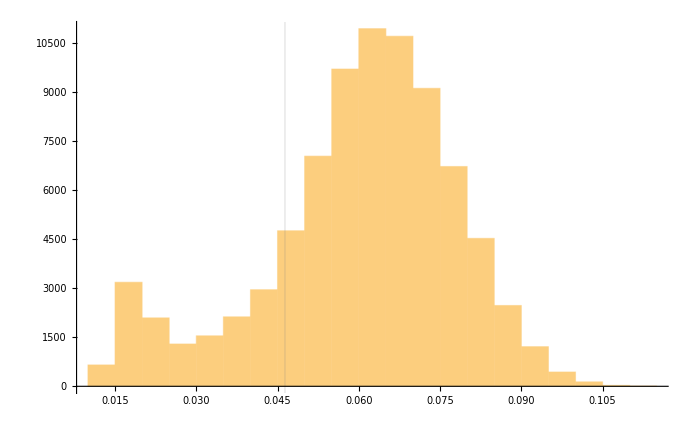

```mathematica
Histogram[erad,GridLines->{{1-156.3/163.9}}]
```

### Fit at 10M

#### n=1 at t=10M aligning

```mathematica
tfit=10;
```

```mathematica
tmax = Table[
   TimeOfMaximum[
    sxsrhsv1[[i, 1,Round[(Length@sxsrhsv1[[i, 1]])/2] ;; -1]]], {i, Length@tag}];
tmax = Join[{tmax}, {tmax}, {tmax}, {tmax}];
```

```mathematica
(* Here start the α0,α1 contours*)
ansall=Table[
mysxscase22modeRD[index]=
Table[t0[index]=tmax[[i,index]];Select[sxsrhsv1[[index,i]],#[[1]]≥ tmax[[i,index]]&]/.{tt_,yy_}->{tt-tmax[[i,index]],yy},{i,Length@modes}];
ans=Table[If[modes[[i,1]]==3&&modes[[i,2]]==2,mix=True,mix=False];

OvertoneModel[0,{mf[[index]],af[[index]]},tfit,"Fitα"->{},"Mode"->modes[[i]],"Mixing"->{mix,{2,2}}],{i,Length@modes}],{index,Length@tag}];
```

```mathematica
val022=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[1]]],#[[1]]≥ tfit&,1])[[1,2]],{i,Length@tag}];
val021=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[2]]],#[[1]]≥ tfit&,1])[[1,2]],{i,Length@tag}];
val033=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[3]]],#[[1]]≥ tfit&,1])[[1,2]],{i,Length@tag}];
val044=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[4]]],#[[1]]≥ tfit&,1])[[1,2]],{i,Length@tag}];
```

```mathematica
phs0={val022,val021,val033,val044}
```

{{5.26791,5.24245,5.21523,3.77056,4.74404,3.22585,4.06827,1.60274,2.49001,1.2599,2.49001,4.11534,5.85542,2.04401,2.22446,4.80165,4.72606,6.31153,0.361813,1.54004,3.29644,3.02935,6.23643,6.30832},{5.65647,5.58263,1.30762,0.444318,0.910801,3.3319,3.74426,5.61046,2.95555,2.28493,2.95555,0.546028,1.41171,5.79803,2.73592,0.856108,3.94063,4.70364,1.73734,2.34928,3.22479,3.04549,4.65267,1.54577},{9.33987,8.98792,3.05762,9.53213,4.7119,5.55707,6.81621,6.24093,4.46238,8.83645,4.46238,3.67745,6.29361,6.84283,3.94551,4.66418,7.67779,3.7501,7.36861,2.86942,5.49252,5.06144,3.58924,6.82631},{9.83915,9.69792,9.89774,7.00927,9.13315,6.31677,8.14392,9.7578,5.51628,9.16093,5.51628,8.75921,5.95097,10.9107,5.06498,10.2284,10.1708,7.05445,7.67277,10.0525,7.30534,6.74156,6.88818,7.0244}}

```mathematica
mysxscase22modeRD0sh=Table[mysxscase22modeRD[index][[j]]/.{xx_,yy_}->{xx,yy Exp[-I phs0[[j,index]]]},{index,Length@tag},{j,Length@modes}];
```

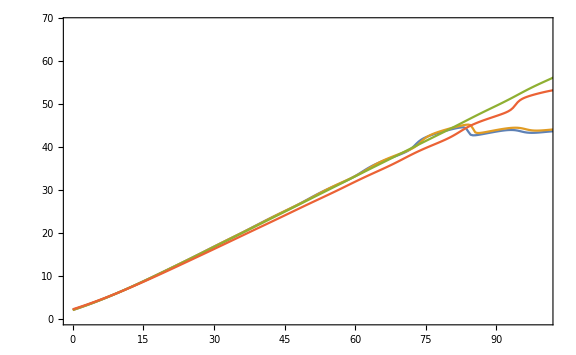

```mathematica
ListLinePlot[{Arg0DStructs@mysxscase22modeRD0sh[[1,1]],Arg0DStructs@mysxscase22modeRD0sh[[2,1]],Arg0DStructs@mysxscase22modeRD0sh[[4,1]],Arg0DStructs@mysxscase22modeRD0sh[[7,1]]},PlotRange->{{0,100},Automatic},ImageSize->Large,Frame->True,GridLines->{{tfit},{2π}},GridLinesStyle->Directive[Orange,Dashed, Thick]]
```

```mathematica
t0ampsdataall=Table[
data=Select[mysxscase22modeRD0sh[[index,j]],#[[1]]≥i&];
ansl=ansall[[index,j]];
cfit=NonlinearModelFit[data,ansl,{x0},t];
amps={x0}/.cfit["BestFitParameters"];

{i,amps},{index,Length@tag},{j,Length@modes},{i,0,20}];
```

```mathematica
t0ampsdataalltest=Table[
data=Select[mysxscase22modeRD0sh[[index,j]],#[[1]]≥i&];
ansl=ansall[[index,j]];
cfit=NonlinearModelFit[data,ansl,{x0},t];
cfitn=Normal@cfit;
amps={x0}/.cfit["BestFitParameters"];

{i,amps,cfitn},{index,Length@tag},{j,Length@modes},{i,tfit,tfit}];
```

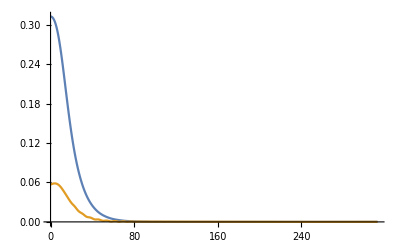

```mathematica
ListLinePlot[{Abs@Select[mysxscase22modeRD0sh[[10,1]],#[[1]]≥0&],Abs@Select[mysxscase22modeRD0sh[[10,3]],#[[1]]≥0&]},PlotRange->All]
```

```mathematica
amps0=Table[Select[(Abs/@(t0ampsdataall[[i,j]])),#[[1]]≥tfit&,1][[1,2]],{i,Length@tag},{j,Length@modes}]
```

{{{0.354997},{3.14998×10^-9},{2.57673×10^-8},{0.00595032}},{{0.353522},{4.06738×10^-9},{2.68557×10^-8},{0.00465637}},{{0.35433},{5.96746×10^-9},{2.21417×10^-8},{0.00313191}},{{0.358089},{0.0142992},{0.0209114},{0.0168801}},{{0.349129},{0.0253962},{0.0356788},{0.0098841}},{{0.323926},{0.0346121},{0.0488841},{0.0126399}},{{0.313175},{0.0385903},{0.0533254},{0.0124853}},{{0.301434},{0.0440153},{0.0593962},{0.0122311}},{{0.285817},{0.0456411},{0.0586782},{0.0166131}},{{0.291702},{0.0475626},{0.0611491},{0.0140543}},{{0.285817},{0.0456411},{0.0586782},{0.0166131}},{{0.268209},{0.0512454},{0.0652034},{0.0148584}},{{0.269451},{0.0514101},{0.0647578},{0.0202417}},{{0.243281},{0.0526417},{0.0677688},{0.0185841}},{{0.225645},{0.0529913},{0.0639306},{0.0201989}},{{0.228117},{0.053796},{0.0646481},{0.0201496}},{{0.197582},{0.0522338},{0.0607462},{0.0228538}},{{0.186829},{0.0518153},{0.0588639},{0.0209822}},{{0.17375},{0.0508676},{0.0563129},{0.0213451}},{{0.172792},{0.0504104},{0.0562366},{0.0212529}},{{0.153012},{0.0470739},{0.0516651},{0.020092}},{{0.136768},{0.0445018},{0.0475968},{0.0196624}},{{0.126962},{0.0423668},{0.0449856},{0.0187634}},{{0.115974},{0.0401392},{0.041692},{0.0179255}}}

```mathematica
{a220d,a210d,a330d,a440}={Transpose[{q,amps0[[All,1,1]]}],Transpose[{q,amps0[[All,2,1]]}],Transpose[{q,amps0[[All,3,1]]}],Transpose[{q,amps0[[All,4,1]]}]};
```

```mathematica
datafit3310=Transpose[{a220d[[All,1]],a330d[[All,2]]/a220d[[All,2]]}];
```

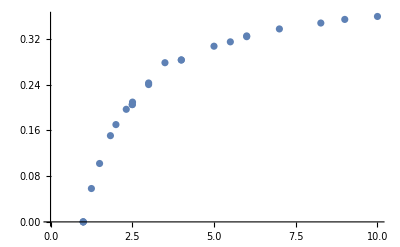

```mathematica
ListPlot[datafit3310]
```

```mathematica
campst0=Table[Flatten[t0ampsdataalltest[[i]],1][[All,2]],{i,Length@tag}];
```

```mathematica
(*From the 32 model: 220, 221, 320, 321, 220*mix,221*mix. Remember to apply all the 2π factors you need!!! *)
```

```mathematica
phase220d=Arg0DStructs@Transpose[{q,campst0[[All,1,1]]}];
phase210d=Arg0DStructs@Transpose[{q,campst0[[All,2,1]]}];
phase330d=Arg0DStructs@Transpose[{q,campst0[[All,3,1]]}];
phase440d=Arg0DStructs@Transpose[{q,campst0[[All,4,1]]}];
phase330220=Transpose[{phase220d[[All,1]],Mod[phase220d[[All,2]]-phase330d[[All,2]],2π]}];
phase210220=Transpose[{phase220d[[All,1]],Mod[phase220d[[All,2]]-phase210d[[All,2]],2π]}];
phase440220=Transpose[{phase220d[[All,1]],Mod[phase220d[[All,2]]-phase440d[[All,2]],2π]}];
```

```mathematica
phfit=Normal@NonlinearModelFit[Select[phase330220,#[[1]]≥1.1 &],aa /(qq^2+cc^2)+bb,{aa,bb,cc},qq,MaxIterations->Infinity]
```

2.55109+8.35567/(8.83957+qq^2)

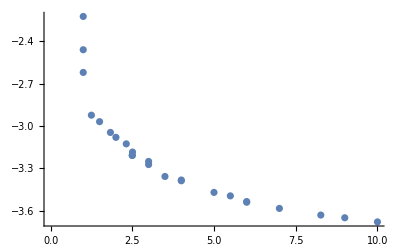

```mathematica
(* at t=10 *)
ListPlot[Transpose[{phase220d[[All,1]],phase220d[[All,2]]-phase330d[[All,2]]}]]
```

```mathematica
corrfactor=Table[(ωlmnPy[3,3,0,mf[[i,1]],af[[i]]][[1]]-ωlmnPy[2,2,0,mf[[i,1]],af[[i]]][[1]])*10,{i,Length@af}]
```

{3.2393,3.2393,3.2393,3.22061,3.18008,3.11531,3.08178,3.02196,2.9893,2.98815,2.9893,2.91121,2.91091,2.8452,2.79074,2.79015,2.70602,2.67278,2.64407,2.64398,2.59685,2.55147,2.53015,2.5057}

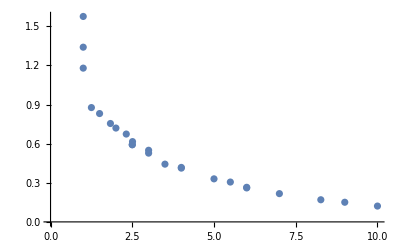

```mathematica
(* at t=0 corrected from t=10 *)
ListPlot[Transpose[{phase220d[[All,1]],phase220d[[All,2]]-phase330d[[All,2]] +3.8}]]
```

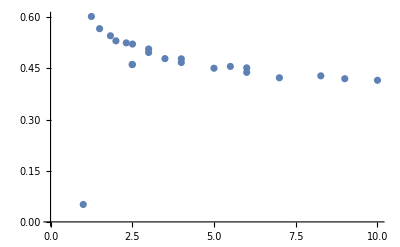

```mathematica
(* at t=0 *)
ListPlot[Transpose[{phase220d[[All,1]],phase220d[[All,2]]-phase330d[[All,2]]}]]
```

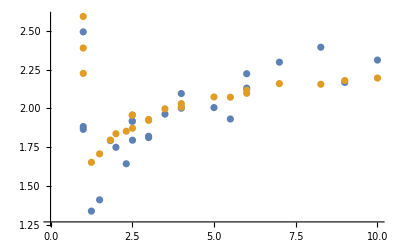

```mathematica
ListPlot[{Transpose[{phase220d[[All,1]],Mod[val033-3ϕq,π]}],Transpose[{phase330d[[All,1]],Mod[phase330d[[All,2]],π]}]}]
```

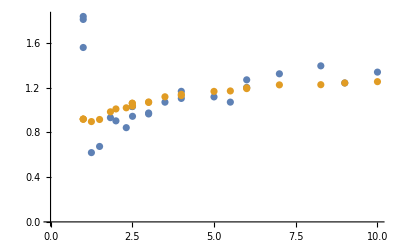

```mathematica
ListPlot[{Transpose[{phase220d[[All,1]],Mod[val022-2ϕq,2π]}],Transpose[{phase220d[[All,1]],Mod[phase220d[[All,2]],2π]-4.5}]}]
```

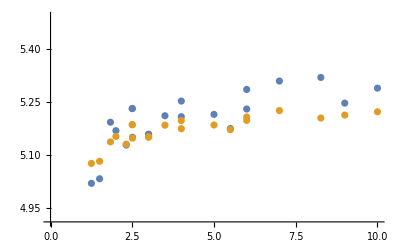

```mathematica
ListPlot[{Transpose[{phase220d[[All,1]],Mod[val021-ϕq,π]+3.9}],Transpose[{phase220d[[All,1]],Mod[phase210d[[All,2]],2π]}]}]
```

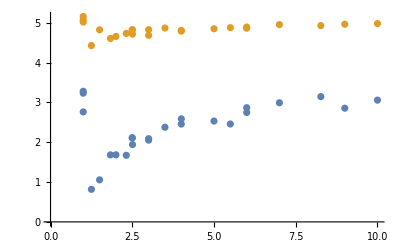

```mathematica
ListPlot[{Transpose[{phase220d[[All,1]],Mod[val044-4ϕq,2π]}],Transpose[{phase220d[[All,1]],Mod[phase440d[[All,2]],2π]}]}]
```

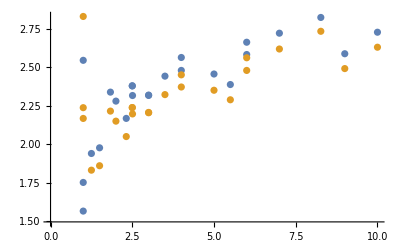

```mathematica
ListPlot[{Transpose[{phase220d[[All,1]],Mod[phase220d[[All,2]]-phase330d[[All,2]]+(val033-3ϕq),π]}],Transpose[{phase220d[[All,1]],3/2(Mod[phase220d[[All,2]]-phase330d[[All,2]]+(val022-2ϕq),π])}]}]
```

```mathematica
val033/val022
```

{1.05413,1.24874,0.674276,-7.94821,-2.72395,1.02727,13.673,-0.00801882,1.24264,-1.02691,1.24264,-7.46668,0.147266,-0.552665,1.26257,-0.961945,1.78609,-0.631661,-0.609996,1.33715,-0.402763,0.649622,-0.586174,0.542367}

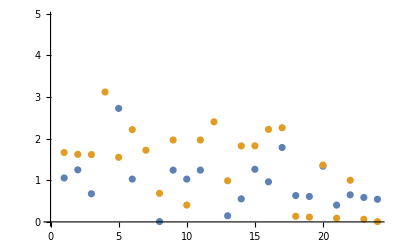

```mathematica
ListPlot[{Abs[val033/val022],Abs[val044/val022]}]
```

```mathematica
pos2=Flatten[Position[q,_?(Abs@(#-1)≥  0.001&)]]
```

{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
ampphase=Transpose[{Mod[phase220d[[All,2]]-phase330d[[All,2]],2π],datafit3310[[All,2]]}][[pos2]]
```

{{3.36021,0.0583972},{3.31435,0.102194},{3.23798,0.150911},{3.20316,0.170273},{3.15709,0.197046},{3.07529,0.2053},{3.09914,0.209628},{3.07529,0.2053},{3.03266,0.243107},{3.0107,0.240332},{2.92624,0.278561},{2.89576,0.283324},{2.90112,0.283399},{2.81341,0.307449},{2.7889,0.315069},{2.74382,0.324103},{2.74851,0.325458},{2.70004,0.337653},{2.65304,0.348011},{2.63392,0.354324},{2.60462,0.359493}}

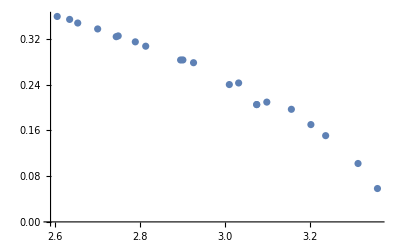

```mathematica
ListPlot[ampphase]
```

#### n=0 at Colin’s time

```mathematica
modes={{2,2},{2,-2},{3,3},{3,-3}}
sxsrhs=Conjugate/@GetAsymptoticMultiMode[#,2,modes,"ReSample"->True]&/@mysxscaserh;
```

{{2,2},{2,2},{3,3},{3,-3}}

```mathematica
ineq=(Ydirect[-2,2,2]==Abs@Ydirect[-2,3,3])/.p->0;
```

```mathematica
inc=Select[t/.NSolve[ineq,{t}],#>0&,1][[1]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.76158

```mathematica
modes
```

{{2,2},{2,-2},{3,3},{3,-3}}

```mathematica
sxsrhsold=Conjugate/@GetAsymptoticMultiMode[#,2,modes,"ReSample"->False]&/@mysxscaserh;
```

```mathematica
(* Making a combined HM waveform. First aligned such that tmax = 0, while the second is not*)
wvcomban=Table[WaveCombine[sxsrhsold[[i]],modes,inc,0,True],{i,Length@sxsrhsold}];
wvcombannal=Table[WaveCombine[sxsrhsold[[i]],modes,inc,0,False],{i,Length@sxsrhsold}];
```

```mathematica
(* Computing the diff time between the peak of the waveform and the peak of the 33mode. Doing so we ensure that tpeak is ≥ t33 *)
tmaxall=Table[TimeOfMaximum[wvcombannal[[i,Round[(Length@wvcombannal[[i]])/2] ;; -1]]],{i,Length@tag}];
tmax33=Table[TimeOfMaximum[sxsrhsold[[i,3]][[Round[(Length@sxsrhsold[[i,1]])/2] ;; -1]]],{i,Length@tag}];
tfit=tmax33-tmaxall +10
```

{27.,28.,26.,13.5,16.,9.5,9.5,11.5,30.,25.5,30.,17.,21.,12.5,31.5,19.5,5.,8.5,26.,30.5,2.,1.,7.5,26.}

```mathematica
(* Taking the postpeak data. *)
waveRD=Table[Select[wvcomban[[i]],#[[1]]≥ 0 &],{i,Length@wvcomban}];
```

```mathematica
(* Spherical harmonics *)
sph22=Ydirect[-2,2,2]/.t->inc/.p-> 0
sph2m2=Ydirect[-2,2,-2]/.t->inc/.p-> 0
sph33=Ydirect[-2,3,3]/.t->inc/.p-> 0
sph3m3=Ydirect[-2,3,-3]/.t->inc/.p-> 0
```

0.468562

0.0120347

-0.468562

0.0120347

```mathematica
(* Ansatz for each NR case at tfit and weighted by tge spherical harmonic *)
ansall=Table[
ov22=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{2,2},"xLabel"->"x22"]*sph22;
ov2m2=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{2,-2},"xLabel"->"x2m2"]*sph2m2;
ov33=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{3,3},"xLabel"->"x33"]*sph33;
ov3m3=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{3,-3},"xLabel"->"x3m3"]*sph3m3;
ov22 +ov2m2+ov33 +ov3m3
,{i,Length@tag}];
```

```mathematica
(* Applying symmetries *)
ansallsym=ansall/.x2m20->Conjugate[x220]/.x3m30->-Conjugate[x330];
```

```mathematica
(* Setting the global phase = 0 at t=0 *)
globphase=Table[(Select[Arg0DStructs[waveRD[[i]]],#[[1]]≥ tfit[[i]]&,1])[[1,2]],{i,Length@tag}];
waveRDal=Table[waveRD[[index]]/.{xx_,yy_}->{xx,yy Exp[-I globphase[[index]]]},{index,Length@tag}];
(*waveRDal=Table[waveRD[[index]]/.{xx_,yy_}->{xx,yy},{index,Length@tag}];*)
waveRDaltfit=Table[Select[waveRDal[[i]],#[[1]]≥ tfit[[i]]&],{i,Length@tag}];
```

```mathematica
tfit[[10]]
```

25.5

```mathematica
fitvals=Table[
anstemp=Simplify[ComplexExpand[ansallsym[[index]]]];
cfit=NonlinearModelFit[Simplify[waveRDaltfit[[index]]],anstemp,{x220,x330},t];
cfitn=Normal@cfit;
amps={x220,x330}/.cfit["BestFitParameters"];

{index,amps,cfitn},{index,Length@tag}];
```

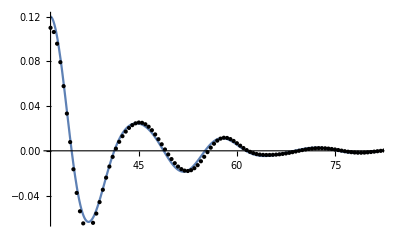

```mathematica
(* Plotting some results *)
ind=15;Plot[Re[fitvals[[ind,-1]]],{t,tfit[[ind]],tfit[[ind]]+50},Epilog->Point[Re@waveRDaltfit[[ind]]],PlotRange->All]
```

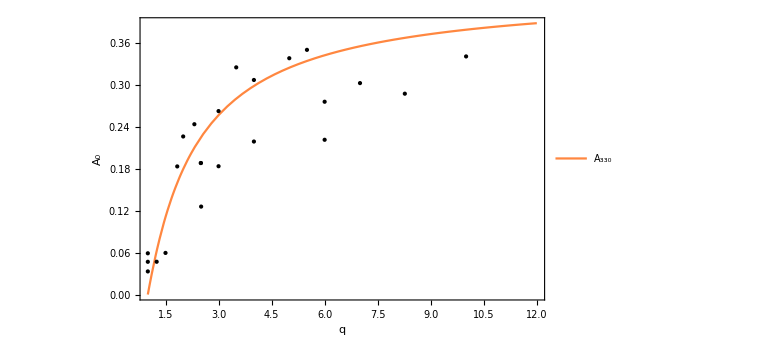

```mathematica
amps0=Abs/@fitvals[[All,2]];
{a220d,a330d}={Transpose[{q,amps0[[All,1]]}],Transpose[{q,amps0[[All,2]]}]};
ar3322=Transpose[{a220d[[All,1]],a330d[[All,2]]/a220d[[All,2]]}];
Plot[{a330[qq]},{qq,1,12},Epilog->{{Point[ar3322]}},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_330","A_220","A_321"},{0.9,0.72}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]
```

```mathematica
(* Now lets compute the phase *)
```

```mathematica
ϕ220=-4.8+ϕq
```

{-5.04987,-5.20191,-5.20191,-5.29736,-4.81237,-5.68432,-5.23501,-3.24701,-6.03727,-3.44846,-6.03727,-5.12728,-4.25869,-6.18745,-6.11244,-4.78386,-4.78034,-3.93784,-3.82585,-3.27562,-5.54394,-5.6756,-3.98797,-3.9879}

```mathematica
phase220d=Arg0DStructs@Transpose[{q,fitvals[[All,2,1]]+ϕ220}];
phase330d=Arg0DStructs@Transpose[{q,fitvals[[All,2,2]]+3/2ϕ220}];
phase330220=Transpose[{phase220d[[All,1]],phase220d[[All,2]]-phase330d[[All,2]]}];
```

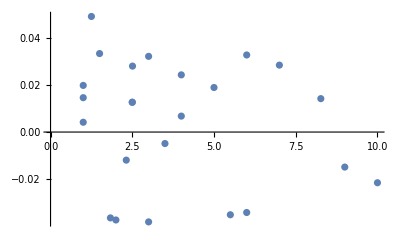

```mathematica
ListPlot[phase330220]
```

```mathematica
phase220d=Arg0DStructs@Transpose[{q,fitvals[[All,2,1]]}];
phase330d=Arg0DStructs@Transpose[{q,fitvals[[All,2,2]]}];
phase330220=Transpose[{phase220d[[All,1]],Mod[phase220d[[All,2]]-phase330d[[All,2]],2π]}];
```

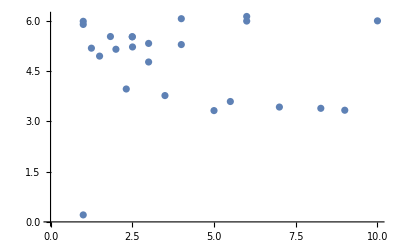

```mathematica
ListPlot[phase330220]
```

```mathematica
η
```

```mathematica
phs=Sqrt[1-4x](0.4795 Exp[3.5587 I]x +1.1736 Exp[1.5679 I]x^2+1.2303 Exp[6.0496 I]x^3)
```

√(1-4 x) ((-0.43839-0.194254 ⅈ) x+(0.00339912+1.1736 ⅈ) x^2+(1.19689-0.284774 ⅈ) x^3)

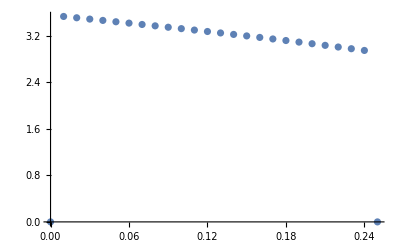

```mathematica
ListPlot[Arg0DStructs@Table[{x,phs},{x,0,0.25,0.01}]/.{xx_,yy_}->{xx,Mod[yy,2π]}]
```

```mathematica
phfit=Normal@NonlinearModelFit[Select[phase330220,#[[1]]≥1.1 &],aa /(qq^2+cc^2)+bb,{aa,bb,cc},qq,MaxIterations->Infinity]
```

1.83092-655.219/(81.862+qq^2)

#### n=0 at Colin’s time with RIT

```mathematica
ineq=(Ydirect[-2,2,2]==Abs@Ydirect[-2,3,3])/.p->0;
```

```mathematica
inc=Select[t/.NSolve[ineq,{t}],#>0&,1][[1]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.76158

```mathematica
modes
```

{{2,2},{2,-2},{3,3},{3,-3}}

```mathematica
(* Making a combined HM waveform. First aligned such that tmax = 0, while the second is not*)
wvcomban=Table[WaveCombine[ritrhs[[i]],modes,inc,0,True],{i,Length@ritrhs}];
wvcombannal=Table[WaveCombine[ritrhs[[i]],modes,inc,0,False],{i,Length@ritrhs}];
```

```mathematica
Length@ritrhs
```

29

```mathematica
(* Computing the diff time between the peak of the waveform and the peak of the 33mode. Doing so we ensure that tpeak is ≥ t33 *)
tmaxall=Table[TimeOfMaximum[wvcombannal[[i,Round[(Length@wvcombannal[[i]])/2] ;; -1]]],{i,Length@tagr}];
tmax33=Table[TimeOfMaximum[ritrhs[[i,3]][[Round[(Length@ritrhs[[i,1]])/2] ;; -1]]],{i,Length@tagr}];
tfit=tmax33-tmaxall +5
```

{-2475.3,-54.1,23.,8.7,3.9,10.4,4.4,3.9,11.7,18.2,6.7,7.7,14.1,13.4,7.4,18.5,18.2,6.2,6.6,-0.2,-0.2,9.5,10.,10.1,2.3,19.2,9.4,1.3,0.9}

```mathematica
(* Taking the postpeak data. *)
waveRD=Table[Select[wvcomban[[i]],#[[1]]≥ 0 &],{i,Length@wvcomban}];
```

```mathematica
(* Spherical harmonics *)
sph22=Ydirect[-2,2,2]/.t->inc/.p-> 0
sph2m2=Ydirect[-2,2,-2]/.t->inc/.p-> 0
sph33=Ydirect[-2,3,3]/.t->inc/.p-> 0
sph3m3=Ydirect[-2,3,-3]/.t->inc/.p-> 0
```

0.468562

0.0120347

-0.468562

0.0120347

```mathematica
(* Ansatz for each NR case at tfit and weighted by tge spherical harmonic *)
ansall=Table[
ov22=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{2,2},"xLabel"->"x22"]*sph22;
ov2m2=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{2,-2},"xLabel"->"x2m2"]*sph2m2;
ov33=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{3,3},"xLabel"->"x33"]*sph33;
ov3m3=OvertoneModel[0,{mf[[i]],af[[i]]},tfit[[i]],"Mode"->{3,-3},"xLabel"->"x3m3"]*sph3m3;
ov22 +ov2m2+ov33 +ov3m3
,{i,Length@tag}];
```

```mathematica
(* Applying symmetries *)
ansallsym=ansall/.x2m20->Conjugate[x220]/.x3m30->-Conjugate[x330];
```

```mathematica
(* Setting the global phase = 0 at t=0 *)
globphase=Table[(Select[Arg0DStructs[waveRD[[i]]],#[[1]]≥ tfit[[i]]&,1])[[1,2]],{i,Length@tag}];
waveRDal=Table[waveRD[[index]]/.{xx_,yy_}->{xx,yy Exp[-I globphase[[index]]]},{index,Length@tag}];

(*waveRDal=Table[waveRD[[index]]/.{xx_,yy_}->{xx,yy},{index,Length@tag}];*)
waveRDaltfit=Table[Select[waveRDal[[i]],#[[1]]≥ tfit[[i]]&],{i,Length@tag}];
```

```mathematica
fitvals=Table[
anstemp=Simplify[ComplexExpand[ansallsym[[index]]]];
cfit=NonlinearModelFit[Simplify[waveRDaltfit[[index]]],anstemp,{x220,x330},t];
cfitn=Normal@cfit;
amps={x220,x330}/.cfit["BestFitParameters"];

{index,amps,cfitn},{index,Length@tag}];
```

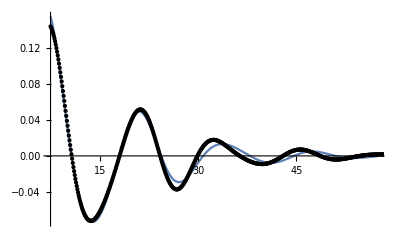

```mathematica
(* Plotting some results *)
ind=15;Plot[Re[fitvals[[ind,-1]]],{t,tfit[[ind]],tfit[[ind]]+50},Epilog->Point[Re@waveRDaltfit[[ind]]],PlotRange->All]
```

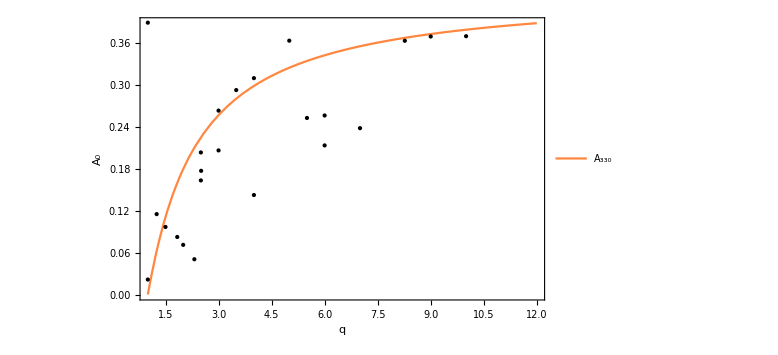

```mathematica
amps0=Abs/@fitvals[[All,2]];
{a220d,a330d}={Transpose[{q,amps0[[All,1]]}],Transpose[{q,amps0[[All,2]]}]};
ar3322=Transpose[{a220d[[All,1]],a330d[[All,2]]/a220d[[All,2]]}];
Plot[{a330[qq]},{qq,1,12},Epilog->{{Point[ar3322]}},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_330","A_220","A_321"},{0.9,0.72}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]
```

```mathematica
(* Now lets compute the phase *)
```

```mathematica
ϕ220=-4.8+ϕq
```

{-5.04987,-5.20191,-5.20191,-5.29736,-4.81237,-5.68432,-5.23501,-3.24701,-6.03727,-3.44846,-6.03727,-5.12728,-4.25869,-6.18745,-6.11244,-4.78386,-4.78034,-3.93784,-3.82585,-3.27562,-5.54394,-5.6756,-3.98797,-3.9879}

```mathematica
phase220d=Arg0DStructs@Transpose[{q,fitvals[[All,2,1]]+ϕ220}];
phase330d=Arg0DStructs@Transpose[{q,fitvals[[All,2,2]]+3/2ϕ220}];
phase330220=Transpose[{phase220d[[All,1]],phase220d[[All,2]]-phase330d[[All,2]]}];
```

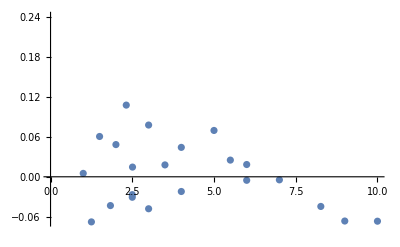

```mathematica
ListPlot[phase330220]
```

```mathematica
phase220d=Arg0DStructs@Transpose[{q,fitvals[[All,2,1]]}];
phase330d=Arg0DStructs@Transpose[{q,fitvals[[All,2,2]]}];
phase330220=Transpose[{phase220d[[All,1]],Mod[phase220d[[All,2]]-phase330d[[All,2]],2π]}];
```

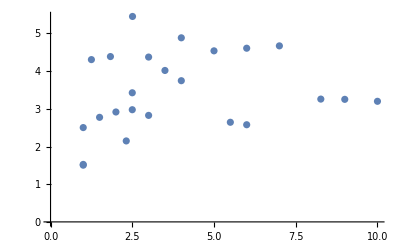

```mathematica
ListPlot[phase330220]
```

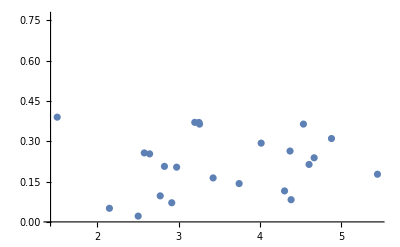

```mathematica
ListPlot@Transpose[{phase330220[[All,2]],a330d[[All,2]]/a220d[[All,2]]}]
```

```mathematica
phfit=Normal@NonlinearModelFit[Select[phase330220,#[[1]]≥1.1 &],aa /(qq^2+cc^2)+bb,{aa,bb,cc},qq,MaxIterations->Infinity]
```

1.83092-655.219/(81.862+qq^2)

## Posteriors

```mathematica
posteriorsamps[samps_,wt_]:=Module[{},

Normal[ExternalEvaluate[Global`session, "resample_equal(np.array("<>ExportString[samps,"RawJSON","Compact"->True]<>"),np.array("<>ExportString[wt,"RawJSON","Compact"->True]<>"))"]]
];
```

```mathematica
contours[kernel_,level_,pars_,varsdom_]:=Module[{pdf,cdf,res},
pdf=Reverse[Sort[Flatten[Table[PDF[kernel,pars],##]&@@varsdom]]];
cdf=Accumulate[pdf]/Total[pdf];
res=pdf[[Flatten[Table[FirstPosition[cdf,p_/;p≥alpha],{alpha,{level}}]]]];
res]
```

```mathematica
Options[Histogram2Line]={"binwidth"->100};
Histogram2Line[dist_,OptionsPattern[]]:=Module[{min,max,binwidth,hlist,dx},
binwidth=OptionValue["binwidth"];
min=Min[dist];
max=Max[dist];
binwidth = Abs[(max-min)/binwidth];
hlist=HistogramList[dist,{min,max,binwidth}];
dx=hlist[[1,2]]-hlist[[1,1]];
hlist/.{xx_,yy_}->{xx,yy/(dx*Total[yy])}
]
```

```mathematica
(* Colin's posteriors *)
myfile="~/Desktop/RDFits_330/KERR-220_330-07MS.hdf"

logw=Import[myfile,{"Datasets","/samples/logwt"}];
logev=ExternalEvaluate[Global`session, "file='/Users/xisco/Desktop/RDFits_330/KERR-220_330-07MS.hdf';
f1 = h5py.File(file,'r'); f1.attrs.get('log_evidence')"];
wt=Exp[logw-logev];
weights=wt/Total[wt];
amp33=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/amp330"}],weights]];
phase33=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/phi330"}],weights]];
phase22=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/phi220"}],weights]];
w33=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/f330"}],weights]];
w22=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/f220"}],weights]];
inclination=posteriorsamps[Import[myfile,{"Datasets","/samples/inclination"}],weights];
finalmass=posteriorsamps[Import[myfile,{"Datasets","/samples/final_mass"}],weights];
```

~/Desktop/RDFits_330/KERR-220_330-07MS.hdf

```mathematica
finalspin=posteriorsamps[Import[myfile,{"Datasets","/samples/final_spin"}],weights];
```

```mathematica
StandardDeviation[finalspin]
```

0.0458062

```mathematica
Median[finalspin]
```

0.870033

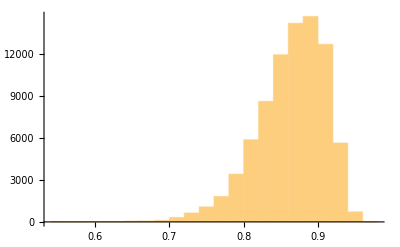

```mathematica
Histogram[finalspin]
```

```mathematica
(* Colin's posteriors *)
myfile="/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/nongr/NONGR-220_330-07MS.hdf"

logw=Import[myfile,{"Datasets","/samples/logwt"}];
logev=ExternalEvaluate[Global`session, "file='/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/nongr/NONGR-220_330-07MS.hdf';
f1 = h5py.File(file,'r'); f1.attrs.get('log_evidence')"];
wt=Exp[logw-logev];
weights=wt/Total[wt];
amp33ngr=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/amp330"}],weights]];
phase33ngr=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/phi330"}],weights]];
phase22ngr=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/phi220"}],weights]];
freq220=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/f220"}],weights]];
freq330=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/f330"}],weights]];
freq330=Normal[posteriorsamps[Import[myfile,{"Datasets","/samples/f330"}],weights]];
```

/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/nongr/NONGR-220_330-07MS.hdf

```mathematica
amp33distngr=SmoothKernelDistribution[Normal[amp33ngr]];
phasediff=Mod[phase22ngr-phase33ngr,2π];
phasedistngr=SmoothKernelDistribution[Mod[phasediff,2π]];
freq220dist=SmoothKernelDistribution[freq220];
freq330dist=SmoothKernelDistribution[freq330];
```

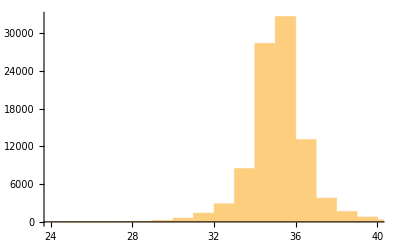

```mathematica
Histogram[freq330-freq220]
```

```mathematica
phaseamp=SmoothKernelDistribution[Transpose[{Normal[amp33],Mod[phase22-phase33,2π]}]];
phaseampngr=SmoothKernelDistribution[Transpose[{Normal[amp33ngr],Mod[phase22ngr-phase33ngr,2π]}]];
```

```mathematica
χfun[x_,y_,fun_]:= -2 Log[PDF[fun,{x,y}]]
```

```mathematica
chi2=NMinimize[{χfun[x,y,phaseamp],0.001≤ x≤0.4, 0<=y≤2π},{x,y}][[1]]
```

-3.532

```mathematica
chi2ngr=NMinimize[{χfun[x,y,phaseampngr],0.001≤ x≤0.3, 0<=y≤2π},{x,y}][[1]]
```

-3.04448

```mathematica
fact=fNU[35,330]*2π
phase[qq_,t_]:=2.551092133630567+8.355670911569911/(8.839571559719866+qq^2)-fact *t
```

0.357371

```mathematica
tab1=Table[{phase[qq,10-tNR[0.006,310]],a330[qq]},{qq,1,10,0.01}];
tab2=Table[{phase[qq,10-tNR[0.007,330]],a330[qq]},{qq,1,10,0.01}];
tab3=Table[{phase[qq,10-tNR[0.008,350]],a330[qq]},{qq,1,10,0.01}];
```

```mathematica
tab1=Table[{Mod[phase[qq,-(tNR[0.039,310]-10+tNR[0.006,310])]-3,2π],a330[qq]},{qq,1,10,0.01}];
tab2=Table[{Mod[phase[qq,-(tNR[0.039,330]-10+tNR[0.007,330])],2π]-3,a330[qq]},{qq,1,10,0.01}];
tab3=Table[{Mod[phase[qq,-(tNR[0.039,330]-10+tNR[0.008,350])]-3,2π],a330[qq]},{qq,1,10,0.01}];
```

```mathematica
itfun=Interpolation/@{tab1,tab2,tab3}
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

InterpolatingFunction::dmval: Input value {0.700088} lies outside the range of data in the interpolating function. Extrapolation will be used.

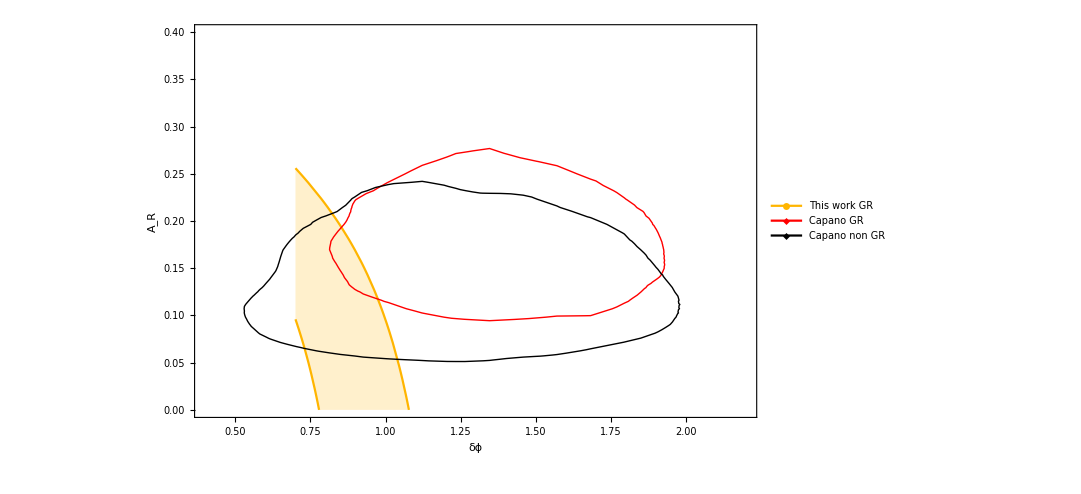

```mathematica
c1=ContourPlot[χfun[x,y,phaseamp],{y,Min[phasediff],Max[phasediff]},{x,0,Max[Normal[amp33]]},ContourShading->None,ContourStyle->Red,Contours->{chi2+2.3},PlotLegends->Placed[LineLegend[{Style["Capano GR",24]},LegendMarkers->{{markers[[3]],0.05},{markers[[1]],0.05},{markers[[2]],0.05}}],{0.8,0.8}]];
c2=ContourPlot[χfun[x,y,phaseampngr],{y,Min[phasediff],Max[phasediff]},{x,Min[Normal[amp33ngr]],Max[Normal[amp33ngr]]},ContourShading->None,Contours->{chi2ngr+2.3},PlotLegends->Placed[LineLegend[{Style["Capano non GR",24]},LegendLayout->{"Column",3},LegendMarkers->{{markers[[3]],0.05},{markers[[1]],0.05},{markers[[2]],0.05}}],{0.8,0.73}]];
lp=Plot[{itfun[[1]][x],itfun[[2]][x],itfun[[3]][x]},{x,0.7,5},Filling->{1->{3}},PlotRange->{{0.4,2.2},{0,0.4}},Frame->True,FrameLabel->{"δϕ","A_R"},Frame->True,FrameStyle->Directive[Black,Bold,20],GridLines->Full,PlotStyle->colors[[4;;4]],
LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]},ImageSize->800,PlotLegends->Placed[LineLegend[{Style["This work GR",24]},LegendLayout->{"Column",3},LegendMarkers->{{markers[[1]],0.05},{markers[[1]],0.05},{markers[[2]],0.05}}],{0.8,0.88}]];
l4=ListPlot[ampphase/.{xx_,yy_}->{xx-fact(10-tNR[0.007,330]),yy}];
lp=Show[lp,c1,c2]
```

```mathematica
Export["~/Desktop/RDFits_330/Aratio_phase.pdf",lp]
```

~/Desktop/RDFits_330/Aratio_phase.pdf

```mathematica
myfile="/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/reweighted/REWEIGHTED_IMR-XPHM.hdf"
logw=Import[myfile,{"Datasets","/samples/logwt"}];
logev=ExternalEvaluate[Global`session, "file='/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/reweighted/REWEIGHTED_IMR-XPHM.hdf';
f1 = h5py.File(file,'r'); f1.attrs.get('log_evidence')"];
wt=Exp[logw-logev];
weights=wt/Total[wt];
qdist=Import[myfile,{"Datasets","/samples/q"}];
```

/Users/xisco/mount/Atlas/sio/git/BH-Spectroscopy-GW190521/posteriors/reweighted/REWEIGHTED_IMR-XPHM.hdf